```mathematica
SetDirectory@NotebookDirectory[];
Quiet@Remove["Global`*"];
Needs["ErrorBarPlots`"];
```

```mathematica
GeoGraphics[GeoMarker[{{44.018089,-73.168445},{43.862657,-72.766778}}]]
```

-Graphics-

```mathematica
DateandTime = Table[DateObject[{2019,1,20,i}],{i,00,48}];
(*DateandTime = Table[DateObject[{2019,1,20,i}],{i,12,18,03}];*)
```

```mathematica
microphysicslist={"M2M","THOM","WDM6","MILL","GODD"};
```

### Snow Accumulation Data

#### Middlebury

```mathematica
(*Plot if we assume 10:1 snow liquid ratio*)
```

```mathematica
Morrison2momentaccummidd=Partition[Flatten[Import["Data_Files/midd_accum_data.txt", "CSV"]],49];
meanM2Mmidd=Mean[Morrison2momentaccummidd];(* Data is output as mm, but we can simply convert to cm, since we must multiply each datapoint by 10 because we assume a 10:1 snow liquid ratio. So our data work as cm. *)
M2Maccumsnowtimes=Transpose[{DateandTime,meanM2Mmidd}];
Thompsonaccummidd=Partition[Flatten[Import["Data_Files/midd_accum_dataTHOM.txt", "CSV"]],49];
meanTHOMmidd=Mean[Thompsonaccummidd];
Thomaccumsnowtimes = Transpose[{DateandTime, meanTHOMmidd}];
WDM6accummidd=Partition[Flatten[Import["Data_Files/midd_accum_dataWDM6.txt", "CSV"]],49];
meanWDM6midd=Mean[WDM6accummidd];
WDM6accumsnowtimes = Transpose[{DateandTime, meanWDM6midd}];
Millbrandtaccummidd=Partition[Flatten[Import["Data_Files/midd_accum_dataMillbrandt.txt", "CSV"]],49];
meanmillbrandtmidd=Mean[Millbrandtaccummidd];
Millbrandtaccumsnowtimes = Transpose[{DateandTime, meanmillbrandtmidd}];
Goddardaccummidd=Partition[Flatten[Import["Data_Files/midd_accum_dataGoddard.txt", "CSV"]],49];
meangoddmidd=Mean[Goddardaccummidd];
Goddardaccumsnowtimes = Transpose[{DateandTime, meangoddmidd}];
```

```mathematica
Obs=ConstantArray[38.1, 49];
```

```mathematica
Length[meanM2Mmidd];
```

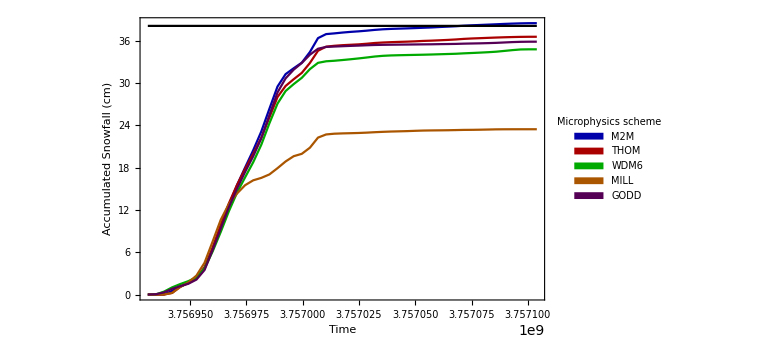

```mathematica
Accumsnowplot=DateListPlot[{meanM2Mmidd,meanTHOMmidd,meanWDM6midd, meanmillbrandtmidd,meangoddmidd,Obs},{2019,1,20,00},Frame->True,FrameLabel->{"Time", "Accumulated Snowfall (cm)"},PlotStyle->{Darker[Blue],Darker[Red],Darker[Green],Darker[Orange],Darker[Purple],Black},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman") }, Joined->True,GridLines->None
,PlotRange -> {{Automatic,Automatic},{0,Automatic}},ImageSize->Large,PlotLegends->SwatchLegend[{"M2M","THOM","WDM6", "MILL","GODD"}, LegendLabel ->"Microphysics scheme", LegendFunction->"Frame"] ]
```

```mathematica
Export["accumsnowplot.png", Accumsnowplot]
```

accumsnowplot.png

```mathematica
meanM2Mmidd;
```

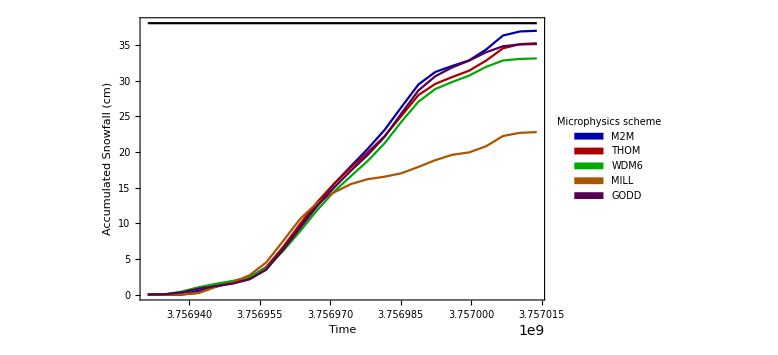

```mathematica
Accumsnowplotday1=DateListPlot[{meanM2Mmidd⟦1;;24⟧,meanTHOMmidd⟦1;;24⟧,meanWDM6midd⟦1;;24⟧, meanmillbrandtmidd⟦1;;24⟧,meangoddmidd⟦1;;24⟧,Obs},{{2019,1,20,00},{2019,1,20,23}},Frame->True,FrameLabel->{"Time", "Accumulated Snowfall (cm)"},PlotStyle->{Darker[Blue],Darker[Red],Darker[Green],Darker[Orange],Darker[Purple],Black},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman") }, Joined->True,GridLines->None
,PlotRange -> {{Automatic,Automatic},{0,Automatic}},ImageSize->Large,PlotLegends->SwatchLegend[{"M2M","THOM","WDM6", "MILL","GODD"}, LegendLabel ->"Microphysics scheme", LegendFunction->"Frame"] ]
```

#### Now this includes Convective precip “SNOWC”

```mathematica
Morrison2momentaccummidd=Partition[Flatten[Import["Data_Files/midd_accum_dataM2Mc.txt", "CSV"]],49];
meanM2Mmidd=Mean[Morrison2momentaccummidd];(* Data is output as mm, but we can simply convert to cm, since we must multiply each datapoint by 10 because we assume a 10:1 snow liquid ratio. So our data work as cm. *)
M2Maccumsnowtimes=Transpose[{DateandTime,meanM2Mmidd}];
Thompsonaccummidd=Partition[Flatten[Import["Data_Files/midd_accum_dataTHOMc.txt", "CSV"]],49];
meanTHOMmidd=Mean[Thompsonaccummidd];
Thomaccumsnowtimes = Transpose[{DateandTime, meanTHOMmidd}];
WDM6accummidd=Partition[Flatten[Import["Data_Files/midd_accum_dataWDM6c.txt", "CSV"]],49];
meanWDM6midd=Mean[WDM6accummidd];
WDM6accumsnowtimes = Transpose[{DateandTime, meanWDM6midd}];
Millbrandtaccummidd=Partition[Flatten[Import["Data_Files/midd_accum_dataMILLc.txt", "CSV"]],49];
meanmillbrandtmidd=Mean[Millbrandtaccummidd];
Millbrandtaccumsnowtimes = Transpose[{DateandTime, meanmillbrandtmidd}];
GODDaccummidd=Partition[Flatten[Import["Data_Files/midd_accum_dataGODDc.txt", "CSV"]],49];
meanGODDmidd=Mean[GODDaccummidd];
GODDaccumsnowtimes = Transpose[{DateandTime, meanGODDmidd}];
```

```mathematica
{StandardDeviation[Table[Morrison2momentaccummidd⟦number⟧⟦24⟧,{number,1,5}]],StandardDeviation[Table[Thompsonaccummidd⟦number⟧⟦24⟧,{number,1,5}]],StandardDeviation[Table[WDM6accummidd⟦number⟧⟦24⟧,{number,1,5}]],StandardDeviation[Table[Millbrandtaccummidd⟦number⟧⟦24⟧,{number,1,5}]],StandardDeviation[Table[GODDaccummidd⟦number⟧⟦24⟧,{number,1,5}]]}
```

{1.8537,3.11085,2.8374,2.42511,4.65174}

```mathematica
{Max[meanM2Mmidd⟦1;;24⟧],Max[meanTHOMmidd⟦1;;24⟧],Max[meanmillbrandtmidd⟦1;;24⟧],Max[meanWDM6midd⟦1;;24⟧],Max[meanGODDmidd⟦1;;24⟧]}
```

{38.016,36.2572,23.7894,34.1349,36.1497}

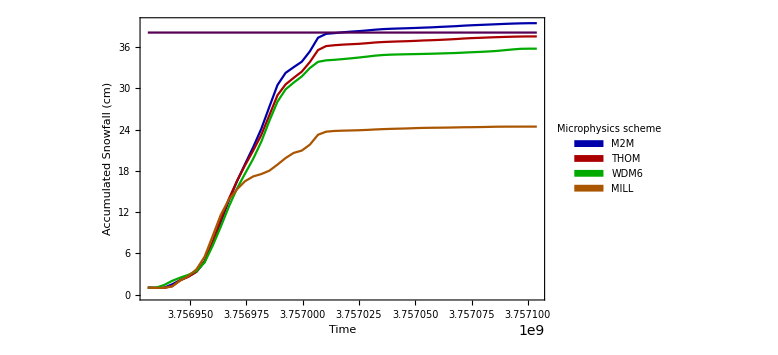

```mathematica
AccumsnowplotC=DateListPlot[{meanM2Mmidd,meanTHOMmidd,meanWDM6midd, meanmillbrandtmidd,Obs},{2019,1,20,00},Frame->True,FrameLabel->{"Time", "Accumulated Snowfall (cm)"},PlotStyle->{Darker[Blue],Darker[Red],Darker[Green],Darker[Orange],Darker[Purple],Black},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman") }, Joined->True,GridLines->None
,PlotRange -> {{Automatic,Automatic},{0,Automatic}},ImageSize->Large,PlotLegends->SwatchLegend[{"M2M","THOM","WDM6", "MILL"}, LegendLabel ->"Microphysics scheme", LegendFunction->"Frame"] ]
```

```mathematica
AccumsnowplotCday1=DateListPlot[{meanM2Mmidd,meanTHOMmidd,meanWDM6midd, meanmillbrandtmidd},{{2019,1,20,00},{2019,1,20,23}},Frame->True,FrameLabel->{"Time", "Accumulated Snowfall (cm)"},PlotStyle->{Darker[Blue],Darker[Red],Darker[Green],Darker[Orange],Darker[Purple],Black},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman") }, Joined->True,GridLines->None
,PlotRange -> {{Automatic,Automatic},{0,Automatic}},ImageSize->Large,PlotLegends->SwatchLegend[{"M2M","THOM","WDM6", "MILL"}, LegendLabel ->"Microphysics scheme", LegendFunction->"Frame"] ];
```

#### Rochester

```mathematica
Morrison2momentaccumroch=Partition[Flatten[Import["Data_Files/roch_accum_dataM2M.txt", "CSV"]],49];
meanM2Mroch=Mean[Morrison2momentaccumroch];(* Data is output as mm, but we can simply convert to cm, since we must multiply each datapoint by 10 because we assume a 10:1 snow liquid ratio. So our data work as cm. *)
M2Maccumsnowtimes=Transpose[{DateandTime,meanM2Mroch}];
```

```mathematica
Thompsonaccumroch=Partition[Flatten[Import["Data_Files/roch_accum_dataTHOM.txt", "CSV"]],49];
meanTHOMroch=Mean[Thompsonaccumroch];
Thomaccumsnowtimes = Transpose[{DateandTime, meanTHOMroch}];
```

```mathematica
WDM6accumroch=Partition[Flatten[Import["Data_Files/roch_accum_dataWDM6.txt", "CSV"]],49];
meanWDM6roch=Mean[WDM6accumroch];
WDM6accumsnowtimes = Transpose[{DateandTime, meanWDM6roch}];
```

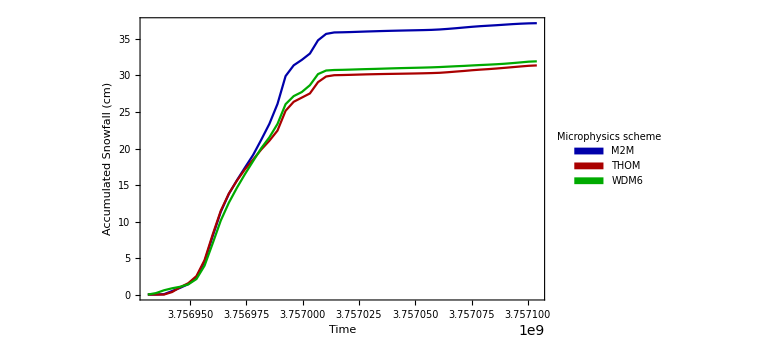

```mathematica
Accumsnowplot=DateListPlot[{meanM2Mroch,meanTHOMroch,meanWDM6roch},{2019,1,20,00},Frame->True,FrameLabel->{"Time", "Accumulated Snowfall (cm)"},PlotStyle->{Darker[Blue],Darker[Red],Darker[Green]},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman") }, Joined->True,GridLines->None
,PlotRange -> {{Automatic,Automatic},{0,Automatic}},ImageSize->Large,PlotLegends->SwatchLegend[{"M2M","THOM","WDM6"}, LegendLabel ->"Microphysics scheme", LegendFunction->"Frame"] ]
```

```mathematica
Morrison2momentaccumroch=Partition[Flatten[Import["Data_Files/roch_accum_dataMORRc.txt", "CSV"]],49];
meanM2Mroch=Mean[Morrison2momentaccumroch];(* Data is output as mm, but we can simply convert to cm, since we must multiply each datapoint by 10 because we assume a 10:1 snow liquid ratio. So our data work as cm. *)
M2Maccumsnowtimes=Transpose[{DateandTime,meanM2Mroch}];
Thompsonaccumroch=Partition[Flatten[Import["Data_Files/roch_accum_dataTHc.txt", "CSV"]],49];
meanTHOMroch=Mean[Thompsonaccumroch];
Thomaccumsnowtimes = Transpose[{DateandTime, meanTHOMroch}];
WDM6accumroch=Partition[Flatten[Import["Data_Files/roch_accum_dataWDM6c.txt", "CSV"]],49];
meanWDM6roch=Mean[WDM6accumroch];
WDM6accumsnowtimes = Transpose[{DateandTime, meanWDM6roch}];
Millbrandtaccumroch=Partition[Flatten[Import["Data_Files/roch_accum_dataMILLc.txt", "CSV"]],49];
meanmillbrandtroch=Mean[Millbrandtaccumroch];
Millbrandtaccumsnowtimes = Transpose[{DateandTime, meanmillbrandtroch}];
GODDaccumroch=Partition[Flatten[Import["Data_Files/roch_accum_dataGODDc.txt", "CSV"]],49];
meanGODDroch=Mean[GODDaccumroch];
GODDaccumsnowtimes = Transpose[{DateandTime, meanGODDroch}];
```

```mathematica
{Max[meanM2Mroch⟦1;;24⟧],Max[meanTHOMroch⟦1;;24⟧],Max[meanmillbrandtroch⟦1;;24⟧],Max[meanWDM6roch⟦1;;24⟧],Max[meanGODDroch⟦1;;24⟧]}
```

{35.8939,30.0387,19.6767,30.7515,30.6225}

```mathematica
{StandardDeviation[Table[Morrison2momentaccumroch⟦number⟧⟦24⟧,{number,1,5}]],StandardDeviation[Table[Thompsonaccumroch⟦number⟧⟦24⟧,{number,1,5}]],StandardDeviation[Table[WDM6accumroch⟦number⟧⟦24⟧,{number,1,5}]],StandardDeviation[Table[Millbrandtaccumroch⟦number⟧⟦24⟧,{number,1,5}]],StandardDeviation[Table[GODDaccumroch⟦number⟧⟦24⟧,{number,1,5}]]}
```

{1.86749,2.22463,2.79282,1.01457,3.59231}

### Accumulated snow plot for my domain of interest

```mathematica
(*Here I avg all values together... this relates well to my precip maps*)
```

```mathematica
allsnowaccumM2M=Replace[Flatten[Import["Data_Files/avg_accum_snowM2M.txt","CSV"]],1->0,{1}];
timeaccumM2M=Partition[allsnowaccumM2M,408];
avgtimeaccumM2M=Table[Mean[timeaccumM2M⟦time⟧],{time,1,24}];
```

```mathematica
maxminM2M={Max[timeaccumM2M⟦24⟧],Min[timeaccumM2M⟦24⟧]} (* Gives the highest total accum and lowest total accum in my domain *)
```

{42.9641,18.302}

```mathematica
allsnowaccumTH=Replace[Flatten[Import["Data_Files/avg_accum_snow.txt","CSV"]],1->0,{1}];
timeaccumTH=Partition[allsnowaccumTH,408];
avgtimeaccumTH=Table[Mean[timeaccumTH⟦time⟧],{time,1,24}];
```

```mathematica
maxminTH={Max[timeaccumTH⟦24⟧],Min[timeaccumTH⟦24⟧]}
```

{38.1112,16.8072}

```mathematica
allsnowaccumWDM6=Replace[Flatten[Import["Data_Files/avg_accum_snowWDM6.txt","CSV"]],1->0,{1}];
timeaccumWDM6=Partition[allsnowaccumWDM6,408];
avgtimeaccumWDM6=Table[Mean[timeaccumWDM6⟦time⟧],{time,1,24}];
```

```mathematica
maxminWDM6={Max[timeaccumWDM6⟦24⟧],Min[timeaccumWDM6⟦24⟧]}
```

{37.4896,14.3178}

```mathematica
allsnowaccumMILL=Replace[Flatten[Import["Data_Files/avg_accum_snowMILL.txt","CSV"]],1->0,{1}];
timeaccumMILL=Partition[allsnowaccumMILL,408];
avgtimeaccumMILL=Table[Mean[timeaccumMILL⟦time⟧],{time,1,24}];
```

```mathematica
maxminMILL={Max[timeaccumMILL⟦24⟧],Min[timeaccumMILL⟦24⟧]}
```

{32.7077,7.22925}

```mathematica
allsnowaccumGODD=Replace[Flatten[Import["Data_Files/avg_accum_snowGODD.txt","CSV"]],1->0,{1}];
timeaccumGODD=Partition[allsnowaccumGODD,408];
avgtimeaccumGODD=Table[Mean[timeaccumGODD⟦time⟧],{time,1,24}];
```

```mathematica
maxminGODD={Max[timeaccumGODD⟦24⟧],Min[timeaccumGODD⟦24⟧]}
```

{37.8756,15.4595}

```mathematica
alldomain={timeaccumM2M⟦24⟧,timeaccumTH⟦24⟧,timeaccumWDM6⟦24⟧,timeaccumMILL⟦24⟧,timeaccumGODD⟦24⟧};
```

```mathematica
meansall=Table[Mean[alldomain⟦physics⟧],{physics,1,5}]
```

{29.0446,27.3471,26.4258,20.9812,25.9081}

```mathematica
stdvsall=Table[StandardDeviation[alldomain⟦physics⟧],{physics,1,5}]
```

{4.99973,4.44998,4.45915,6.37363,4.6264}

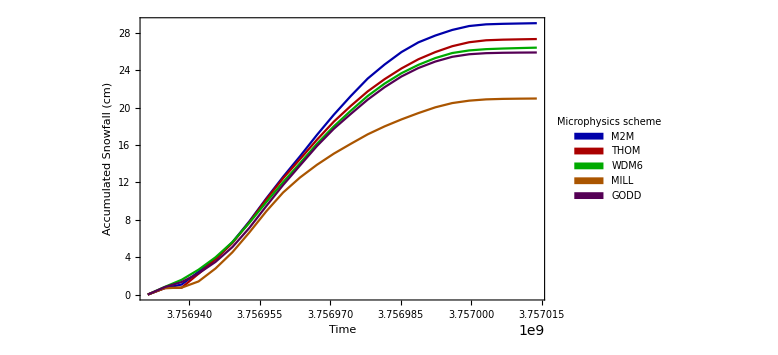

```mathematica
avgAccumsnowplot=DateListPlot[{avgtimeaccumM2M,avgtimeaccumTH,avgtimeaccumWDM6, avgtimeaccumMILL,avgtimeaccumGODD},{2019,1,20,00},Frame->True,FrameLabel->{"Time", "Accumulated Snowfall (cm)"},PlotStyle->{Darker[Blue],Darker[Red],Darker[Green],Darker[Orange],Darker[Purple]},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman") }, Joined->True,GridLines->None
,PlotRange -> {{Automatic,Automatic},{0,Automatic}},ImageSize->Large,PlotLegends->SwatchLegend[{"M2M","THOM","WDM6", "MILL","GODD"}, LegendLabel ->"Microphysics scheme", LegendFunction->"Frame"] ]
```

```mathematica
Export["avgAccumsnowplot.png",avgAccumsnowplot]
```

avgAccumsnowplot.png

### Average accumulated snow including Graupel

```mathematica
allsnowaccumM2M=Replace[Flatten[Import["Data_Files/avg_accum_snowM2Mg.txt","CSV"]],1->0,{1}];
timeaccumM2M=Partition[allsnowaccumM2M,408];
avgtimeaccumM2M=Table[Mean[timeaccumM2M⟦time⟧],{time,1,24}];
allsnowaccumTH=Replace[Flatten[Import["Data_Files/avg_accum_snowTHOMg.txt","CSV"]],1->0,{1}];
timeaccumTH=Partition[allsnowaccumTH,408];
avgtimeaccumTH=Table[Mean[timeaccumTH⟦time⟧],{time,1,24}];
allsnowaccumWDM6=Replace[Flatten[Import["Data_Files/avg_accum_snowWDM6g.txt","CSV"]],1->0,{1}];
timeaccumWDM6=Partition[allsnowaccumWDM6,408];
avgtimeaccumWDM6=Table[Mean[timeaccumWDM6⟦time⟧],{time,1,24}];
allsnowaccumMILL=Replace[Flatten[Import["Data_Files/avg_accum_snowMILLg.txt","CSV"]],1->0,{1}];
timeaccumMILL=Partition[allsnowaccumMILL,408];
avgtimeaccumMILL=Table[Mean[timeaccumMILL⟦time⟧],{time,1,24}];
allsnowaccumGODD=Replace[Flatten[Import["Data_Files/avg_accum_snowGODDg.txt","CSV"]],1->0,{1}];
timeaccumGODD=Partition[allsnowaccumGODD,408];
avgtimeaccumGODD=Table[Mean[timeaccumGODD⟦time⟧],{time,1,24}];
```

```mathematica
alldomain={timeaccumM2M⟦24⟧,timeaccumTH⟦24⟧,timeaccumWDM6⟦24⟧,timeaccumMILL⟦24⟧,timeaccumGODD⟦24⟧};
```

```mathematica
withgraupel=Table[Mean[alldomain⟦physics⟧],{physics,1,5}]
```

{29.1562,28.5509,28.9628,28.2281,27.1324}

```mathematica
stdvsgraupel=Table[StandardDeviation[alldomain⟦physics⟧],{physics,1,5}]
```

{4.96608,4.00781,5.2237,4.67146,4.24561}

```mathematica
percentgraupel=((withgraupel-meansall)/withgraupel)*100
```

{0.382811,4.21641,8.75974,25.6726,4.51245}

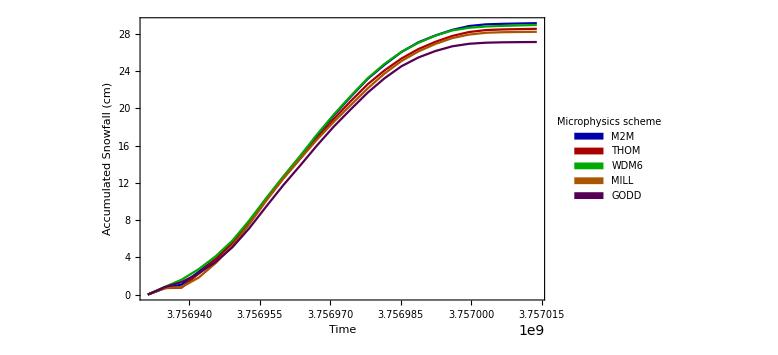

```mathematica
avgAccumsnowplot=DateListPlot[{avgtimeaccumM2M,avgtimeaccumTH,avgtimeaccumWDM6, avgtimeaccumMILL,avgtimeaccumGODD},{2019,1,20,00},Frame->True,FrameLabel->{"Time", "Accumulated Snowfall (cm)"},PlotStyle->{Darker[Blue],Darker[Red],Darker[Green],Darker[Orange],Darker[Purple]},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman") }, Joined->True,GridLines->None
,PlotRange -> {{Automatic,Automatic},{0,Automatic}},ImageSize->Large,PlotLegends->SwatchLegend[{"M2M","THOM","WDM6", "MILL","GODD"}, LegendLabel ->"Microphysics scheme", LegendFunction->"Frame"] ]
```

```mathematica
Export["avgAccumsnowplot.png",avgAccumsnowplot]
```

avgAccumsnowplot.png

### Accumulated snow including graupel

#### Middlebury

```mathematica
Morrison2momentaccummidd=Partition[Flatten[Import["Data_Files/midd_accum_dataM2Mg.txt", "CSV"]],49];
meanM2Mmidd=Mean[Morrison2momentaccummidd];(* Data is output as mm, but we can simply convert to cm, since we must multiply each datapoint by 10 because we assume a 10:1 snow liquid ratio. So our data work as cm. *)
Thompsonaccummidd=Partition[Flatten[Import["Data_Files/midd_accum_dataTHg.txt", "CSV"]],49];
meanTHOMmidd=Mean[Thompsonaccummidd];
WDM6accummidd=Partition[Flatten[Import["Data_Files/midd_accum_dataWDM6g.txt", "CSV"]],49];
meanWDM6midd=Mean[WDM6accummidd];
Millbrandtaccummidd=Partition[Flatten[Import["Data_Files/midd_accum_dataMILLg.txt", "CSV"]],49];
meanmillbrandtmidd=Mean[Millbrandtaccummidd];
GODDaccummidd=Partition[Flatten[Import["Data_Files/midd_accum_dataGODDg.txt", "CSV"]],49];
meanGODDmidd=Mean[GODDaccummidd];
```

```mathematica
{Max[meanM2Mmidd⟦1;;24⟧],Max[meanTHOMmidd⟦1;;24⟧],Max[meanWDM6midd⟦1;;24⟧],Max[meanmillbrandtmidd⟦1;;24⟧],Max[meanGODDmidd⟦1;;24⟧]}
```

{38.0162,36.4006,36.9937,37.2351,36.4485}

```mathematica
{StandardDeviation[Table[Morrison2momentaccummidd⟦number⟧⟦24⟧,{number,1,5}]],StandardDeviation[Table[Thompsonaccummidd⟦number⟧⟦24⟧,{number,1,5}]],StandardDeviation[Table[WDM6accummidd⟦number⟧⟦24⟧,{number,1,5}]],StandardDeviation[Table[Millbrandtaccummidd⟦number⟧⟦24⟧,{number,1,5}]],StandardDeviation[Table[GODDaccummidd⟦number⟧⟦24⟧,{number,1,5}]]}
```

{1.85364,3.0465,3.14951,1.57968,4.46686}

#### Rochester

```mathematica
Morrison2momentaccumroch=Partition[Flatten[Import["Data_Files/roch_accum_dataM2Mg.txt", "CSV"]],49];
meanM2Mroch=Mean[Morrison2momentaccumroch];(* Data is output as mm, but we can simply convert to cm, since we must multiply each datapoint by 10 because we assume a 10:1 snow liquid ratio. So our data work as cm. *)
Thompsonaccumroch=Partition[Flatten[Import["Data_Files/roch_accum_dataTHg.txt", "CSV"]],49];
meanTHOMroch=Mean[Thompsonaccumroch];
WDM6accumroch=Partition[Flatten[Import["Data_Files/roch_accum_dataWDM6g.txt", "CSV"]],49];
meanWDM6roch=Mean[WDM6accumroch];
Millbrandtaccumroch=Partition[Flatten[Import["Data_Files/roch_accum_dataMILLg.txt", "CSV"]],49];
meanmillbrandtroch=Mean[Millbrandtaccumroch];
GODDaccumroch=Partition[Flatten[Import["Data_Files/roch_accum_dataGODDg.txt", "CSV"]],49];
meanGODDroch=Mean[GODDaccumroch];
```

```mathematica
{Max[meanM2Mroch⟦1;;24⟧],Max[meanTHOMroch⟦1;;24⟧],Max[meanWDM6roch⟦1;;24⟧],Max[meanmillbrandtroch⟦1;;24⟧],Max[meanGODDroch⟦1;;24⟧]}
```

{37.2108,34.8506,37.7414,33.19,34.6775}

```mathematica
{StandardDeviation[Table[Morrison2momentaccumroch⟦number⟧⟦24⟧,{number,1,5}]],StandardDeviation[Table[Thompsonaccumroch⟦number⟧⟦24⟧,{number,1,5}]],StandardDeviation[Table[WDM6accumroch⟦number⟧⟦24⟧,{number,1,5}]],StandardDeviation[Table[Millbrandtaccumroch⟦number⟧⟦24⟧,{number,1,5}]],StandardDeviation[Table[GODDaccumroch⟦number⟧⟦24⟧,{number,1,5}]]}
```

{1.8571,2.78885,3.14057,2.33674,3.53249}

### Snow Water Equivalent

```mathematica
Morrison2momentSWEmidd=Partition[Flatten[Import["Data_Files/midd_SWE_dataM2M.txt", "CSV"]],49];
meanM2Mmidd=Mean[Morrison2momentSWEmidd];(* Units here are kg m^-2*)
M2MSWEsnowtimes=Transpose[{DateandTime,meanM2Mmidd}];
```

```mathematica
ThompsonSWEmidd=Partition[Flatten[Import["Data_Files/midd_SWE_dataTHOM.txt", "CSV"]],49];
meanTHOMmidd=Mean[ThompsonSWEmidd];
ThomSWEsnowtimes = Transpose[{DateandTime, meanTHOMmidd}];
```

```mathematica
WDM6SWEmidd=Partition[Flatten[Import["Data_Files/midd_SWE_dataWDM6.txt", "CSV"]],49];
meanWDM6midd=Mean[WDM6SWEmidd];
WDM6SWEsnowtimes = Transpose[{DateandTime, meanWDM6midd}];
```

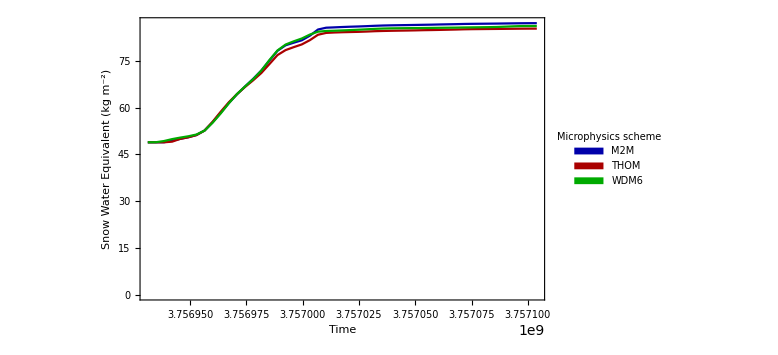

```mathematica
SWEsnowplot=DateListPlot[{meanM2Mmidd,meanTHOMmidd,meanWDM6midd},{2019,1,20,00},Frame->True,FrameLabel->{"Time", "Snow Water Equivalent (kg m^-2)"},PlotStyle->{Darker[Blue],Darker[Red],Darker[Green]},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman") }, Joined->True,GridLines->None
,PlotRange -> {{Automatic,Automatic},{0,Automatic}},ImageSize->Large,PlotLegends->SwatchLegend[{"M2M","THOM","WDM6"}, LegendLabel ->"Microphysics scheme", LegendFunction->"Frame"] ]
```

## All hydrometeor data mixing ratios

```mathematica
(*Note: mixing ratio is defined as g of X per kg of air*)
```

```mathematica
(*As I have it now, I can only get data for one time efficiently in NCL. I need to figure out an effective way to loop through many times to get data for snow mixing ratio. Right now I only have 14:00 UTC *)
```

```mathematica
THOMhydromidd = Partition[Partition[Flatten[Import["Data_Files/midd_hydrometeor_dataTHOM.txt","CSV"]],2],38];
WDM6hydromidd=Partition[Partition[Flatten[Import["Data_Files/midd_hydrometeor_dataWDM6.txt","CSV"]],2],38];
M2Mhydromidd = Partition[Partition[Flatten[Import["Data_Files/midd_hydrometeor_dataM2M.txt","CSV"]],2],38];
```

```mathematica
vaporplotmidd=ListPlot[{M2Mhydromidd⟦1⟧,THOMhydromidd⟦1⟧,WDM6hydromidd⟦1⟧},Frame->True,FrameLabel->{"Vapor mixing ratio (g kg^-1)", "Height (m)"},PlotStyle->{Darker[Blue],Darker[Red],Darker[Green]},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman") }, Joined->True,GridLines->None
,PlotRange -> {{Automatic,Automatic},{0,Automatic}},ImageSize->Large,PlotLegends->SwatchLegend[{"M2M","THOM","WDM6"}, LegendLabel ->"Microphysics scheme", LegendFunction->"Frame"] , Epilog->Inset["Valid: 2019-01-20_14:00:00",{3.5,19500}]];
```

```mathematica
cloudplotmidd=ListPlot[{M2Mhydromidd⟦2⟧,THOMhydromidd⟦2⟧,WDM6hydromidd⟦2⟧},Frame->True,FrameLabel->{"Cloud mixing ratio (g kg^-1)", "Height (m)"},PlotStyle->{Darker[Blue],Darker[Red],Darker[Green]},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman") }, Joined->True,GridLines->None
,PlotRange -> {{Automatic,Automatic},{0,Automatic}},ImageSize->Large,PlotLegends->SwatchLegend[{"M2M","THOM","WDM6"}, LegendLabel ->"Microphysics scheme", LegendFunction->"Frame"] , Epilog->Inset["Valid: 2019-01-20_14:00:00",{0.04,19500}]];
```

```mathematica
rainplotmidd=ListPlot[{M2Mhydromidd⟦3⟧,THOMhydromidd⟦3⟧,WDM6hydromidd⟦3⟧},Frame->True,FrameLabel->{"Rain mixing ratio (g kg^-1)", "Height (m)"},PlotStyle->{Darker[Blue],Darker[Red],Darker[Green]},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman") }, Joined->True,GridLines->None
,PlotRange -> {{Automatic,.000057},{0,Automatic}},ImageSize->Large,PlotLegends->SwatchLegend[{"M2M","THOM","WDM6"}, LegendLabel ->"Microphysics scheme", LegendFunction->"Frame"] , Epilog->Inset["Valid: 2019-01-20_14:00:00",{0.00004,19500}]];
```

```mathematica
iceplotmidd=ListPlot[{M2Mhydromidd⟦4⟧,THOMhydromidd⟦4⟧,WDM6hydromidd⟦4⟧},Frame->True,FrameLabel->{"Ice mixing ratio (g kg^-1)", "Height (m)"},PlotStyle->{Darker[Blue],Darker[Red],Darker[Green]},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman") }, Joined->True,GridLines->None
,PlotRange -> {{0,.152},{0,Automatic}},ImageSize->Large,PlotLegends->SwatchLegend[{"M2M","THOM","WDM6"}, LegendLabel ->"Microphysics scheme", LegendFunction->"Frame"],Epilog->Inset["Valid: 2019-01-20_14:00:00",{0.12,19500}]];
```

```mathematica
snowplotmidd=ListPlot[{M2Mhydromidd⟦6⟧,THOMhydromidd⟦6⟧,WDM6hydromidd⟦6⟧},Frame->True,FrameLabel->{"Snow mixing ratio (g kg^-1)", "Height (m)"},PlotStyle->{Darker[Blue],Darker[Red],Darker[Green]},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman") }, Joined->True,GridLines->None
,PlotRange -> {{Automatic,Automatic},{0,Automatic}},ImageSize->Large,PlotLegends->SwatchLegend[{"M2M","THOM","WDM6"}, LegendLabel ->"Microphysics scheme", LegendFunction->"Frame"] , Epilog->Inset["Valid: 2019-01-20_14:00:00",{0.6,19500}]];
```

```mathematica
graupelplotmidd=ListPlot[{M2Mhydromidd⟦5⟧,THOMhydromidd⟦5⟧,WDM6hydromidd⟦5⟧},Frame->True,FrameLabel->{"Graupel mixing ratio (g kg^-1)", "Height (m)"},PlotStyle->{Darker[Blue],Darker[Red],Darker[Green]},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman") }, Joined->True,GridLines->None
,PlotRange -> {{Automatic,.09},{0,Automatic}},ImageSize->Large,PlotLegends->SwatchLegend[{"M2M","THOM","WDM6"}, LegendLabel ->"Microphysics scheme", LegendFunction->"Frame"] , Epilog->Inset["Valid: 2019-01-20_14:00:00",{0.075,19500}]];
```

```mathematica
GraphicsGrid[{{vaporplotmidd,cloudplotmidd},{rainplotmidd,iceplotmidd},{snowplotmidd, graupelplotmidd}}];
```

```mathematica
listTypes ={"Vapor mixing ratio (g kg^-1)","Cloud mixing ratio (g kg^-1)","Rain mixing ratio (g kg^-1)","Ice mixing ratio (g kg^-1)","Graupel mixing ratio (g kg^-1)","Snow mixing ratio (g kg^-1)"};
listTimes={"Valid: 2019-01-20_04:00:00","Valid: 2019-01-20_08:00:00","Valid: 2019-01-20_12:00:00","Valid: 2019-01-20_16:00:00","Valid: 2019-01-20_20:00:00"};
```

```mathematica
heights = Flatten[Import["Data_Files/midd_heights_THOM.txt","CSV"]];
```

```mathematica
seperatetimesTHOM=Partition[Flatten[Import["Data_Files/midd_hydrometeor_dataTHOM.txt","CSV"]],228];
hydrometeorTHOM=Table[Partition[seperatetimesTHOM⟦i⟧,38],{i,1,6}];
listDataTHOM=Table[Table[Transpose[{hydrometeorTHOM⟦type⟧⟦time⟧,heights}],{type,1,6}],{time,1,6}];
```

```mathematica
seperatetimesWDM6=Partition[Flatten[Import["Data_Files/midd_hydrometeor_dataWDM6times.txt","CSV"]],228];
hydrometeorWDM6=Table[Partition[seperatetimesWDM6⟦i⟧,38],{i,1,6}];
listDataWDM6=Table[Table[Transpose[{hydrometeorWDM6⟦type⟧⟦time⟧,heights}],{type,1,6}],{time,1,6}];
```

```mathematica
seperatetimesM2M=Partition[Flatten[Import["Data_Files/midd_hydrometeor_dataM2Mtimes.txt","CSV"]],228];
hydrometeorM2M=Table[Partition[seperatetimesM2M⟦i⟧,38],{i,1,6}];
listDataM2M=Table[Table[Transpose[{hydrometeorM2M⟦type⟧⟦time⟧,heights}],{type,1,6}],{time,1,6}];
```

```mathematica
(*Do[Print[ListPlot[{listDataM2M⟦time⟧⟦type⟧,listDataTHOM⟦time⟧⟦type⟧,listDataWDM6⟦time⟧⟦type⟧},Frame->True,FrameLabel->{listTypes⟦type⟧, "Height (m)"},PlotStyle->{Darker[Blue],Darker[Red],Darker[Green]},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman") }, Joined->True,GridLines->None
,PlotRange -> {{Automatic,All},{0,Automatic}},ImageSize->Large,PlotLegends->SwatchLegend[{"M2M","THOM","WDM6"}, LegendLabel ->"Microphysics scheme", LegendFunction->"Frame"] , Epilog->Inset[listTimes⟦time-1⟧,{Max[hydrometeorTHOM⟦time⟧⟦type⟧],19500}]]],{type,1,6},{time,2,6}];*)
```

```mathematica
Manipulate[ListPlot[{listDataM2M⟦time⟧⟦type⟧,listDataTHOM⟦time⟧⟦type⟧,listDataWDM6⟦time⟧⟦type⟧},Frame->True,FrameLabel->{listTypes⟦type⟧, "Height (m)"},PlotStyle->{Darker[Blue],Darker[Red],Darker[Green]},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman") }, Joined->True,GridLines->None
,PlotRange -> {{Automatic,All},{0,Automatic}},ImageSize->Large,PlotLegends->SwatchLegend[{"M2M","THOM","WDM6"}, LegendLabel ->"Microphysics scheme", LegendFunction->"Frame"] , Epilog->Inset[listTimes⟦time-1⟧,{Max[hydrometeor⟦type⟧⟦time⟧],19500}]],{type,1,6,1},{time,2,6,1}];
```

## All hydrometeor data mixing ratios

```mathematica
(*good - just need to figure out averages*)
```

```mathematica
(*Note: mixing ratio is defined as g of X per kg of air*)
```

```mathematica
(*As I have it now, I can only get data for one time efficiently in NCL. I need to figure out an effective way to loop through many times to get data for snow mixing ratio. Right now I only have 14:00 UTC *)
```

```mathematica
listTypes ={"Vapor mixing ratio (g kg^-1)","Cloud mixing ratio (g kg^-1)","Rain mixing ratio (g kg^-1)","Ice mixing ratio (g kg^-1)","Graupel mixing ratio (g kg^-1)","Snow mixing ratio (g kg^-1)"};
listTimes={"Valid: 2019-01-20_00:00:00","Valid: 2019-01-20_01:00:00","Valid: 2019-01-20_02:00:00","Valid: 2019-01-20_03:00:00","Valid: 2019-01-20_04:00:00","Valid: 2019-01-20_05:00:00","Valid: 2019-01-20_06:00:00","Valid: 2019-01-20_07:00:00","Valid: 2019-01-20_08:00:00","Valid: 2019-01-20_09:00:00","Valid: 2019-01-20_10:00:00","Valid: 2019-01-20_11:00:00","Valid: 2019-01-20_12:00:00","Valid: 2019-01-20_13:00:00","Valid: 2019-01-20_14:00:00","Valid: 2019-01-20_15:00:00","Valid: 2019-01-20_16:00:00","Valid: 2019-01-20_17:00:00","Valid: 2019-01-20_18:00:00","Valid: 2019-01-20_19:00:00","Valid: 2019-01-20_20:00:00","Valid: 2019-01-20_21:00:00","Valid: 2019-01-20_22:00:00","Valid: 2019-01-20_23:00:00"};
```

```mathematica
seperatetimesTHOM=Partition[Flatten[Import["midd_hydrometeor_dataTHOMtimes1.txt","CSV"]],912];
hydrometeorTHOM=Table[Partition[seperatetimesTHOM⟦i⟧,38],{i,1,6}];
listDataTHOM=Table[Table[Transpose[{hydrometeorTHOM⟦type⟧⟦time⟧,heights}],{type,1,6}],{time,1,24}];
seperatetimesWDM6=Partition[Flatten[Import["midd_hydrometeor_dataWDM6times1.txt","CSV"]],912];
hydrometeorWDM6=Table[Partition[seperatetimesWDM6⟦i⟧,38],{i,1,6}];
listDataWDM6=Table[Table[Transpose[{hydrometeorWDM6⟦type⟧⟦time⟧,heights}],{type,1,6}],{time,1,24}];
seperatetimesM2M=Partition[Flatten[Import["midd_hydrometeor_dataM2Mtimes1.txt","CSV"]],912];
hydrometeorM2M=Table[Partition[seperatetimesM2M⟦i⟧,38],{i,1,6}];
listDataM2M=Table[Table[Transpose[{hydrometeorM2M⟦type⟧⟦time⟧,heights}],{type,1,6}],{time,1,24}];
```

```mathematica
TH=Partition[Flatten[hydrometeorTHOM],912];
WD=Partition[Flatten[hydrometeorWDM6],912];
M2=Partition[Flatten[hydrometeorM2M],912];
formax=Table[{M2⟦i⟧,TH⟦i⟧,WD⟦i⟧},{i,1,6}];
plotRange=Flatten[Table[{Max[formax⟦i⟧]},{i,1,6}]]
```

{4.13323,0.395891,0.000524196,0.147341,0.0994917,0.923967}

```mathematica
Manipulate[ListPlot[{listDataM2M⟦time⟧⟦type⟧,listDataTHOM⟦time⟧⟦type⟧,listDataWDM6⟦time⟧⟦type⟧},Frame->True,FrameLabel->{listTypes⟦type⟧, "Height (m)"},PlotStyle->{Darker[Blue],Darker[Red],Darker[Green]},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman") }, Joined->True,GridLines->None
,PlotRange -> {{Automatic,plotRange⟦type⟧},{0,Automatic}},ImageSize->Large,PlotLegends->SwatchLegend[{"M2M","THOM","WDM6"}, LegendLabel ->"Microphysics scheme", LegendFunction->"Frame"],  Epilog->Inset[Style[listTimes⟦time⟧,FontFamily->"Times New Roman",12],{plotRange⟦type⟧-.17*(plotRange⟦type⟧),19500}]],{type,1,6,1},{time,2,24,1}]
```

Part::partd: Part specification listDataM2M⟦2⟧ is longer than depth of object.

Part::partd: Part specification listDataTHOM⟦2⟧ is longer than depth of object.

Part::partd: Part specification listDataWDM6⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

System`ListPlotsDump`messageshead$5771::prng: Value of option PlotRange -> {{Automatic,plotRange⟦1⟧},{0,Automatic}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

### Same as above, but not focused on just Middlebury, this section of data includes averages for a larger domain - pictured below:

```mathematica
(*The following image highlighted in white is roughly the domain I use for statistics, where as the entire model domain is much larger*)
```

```mathematica
Import["Images/Data_analysis_domain.png"]
```

-Graphics-

Order is (Qv,Qc,Qr,qi,qg,qs)

```mathematica
NgMILL=Flatten[Import["Data_Files/domain_graupel_Ng_dataMILLtimes.txt","CSV"]];
```

```mathematica
Length[NgMILL]
```

372096

```mathematica
NgpartMILL=Partition[NgMILL,15504];
```

```mathematica
seperatetimesheightsNgMILL=Table[Partition[NgpartMILL⟦time⟧,408],{time,1,24}];
```

```mathematica
means=Table[Mean[seperatetimesheightsNgMILL⟦time⟧⟦height⟧],{time,1,24},{height,1,38}];
```

```mathematica
Length[means];
```

```mathematica
Mean[means]
```

{2.17221×10^6,2.16321×10^6,2.14281×10^6,2.095×10^6,2.01273×10^6,1.86845×10^6,1.65171×10^6,1.37562×10^6,1.14206×10^6,1.08837×10^6,1.10578×10^6,1.11851×10^6,988342.,839313.,668860.,485912.,298030.,86777.3,24631.6,19197.3,18981.,15997.2,11233.9,4449.6,2420.85,1151.53,5.00083,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Mean[NgMILL]
```

615836.

```mathematica
Mean[NgpartMILL⟦1⟧]
```

0

```mathematica
t=Flatten[NgpartMILL⟦2;24⟧]
```

{711431.,198026.,71562.8,301093.,160054.,87339.,28319.6,123358.,20221.9,150985.,34390.7,4252.37,21013.2,16701.1,14566.8,2858.84,328.322,994865.,139828.,91366.9,892344.,429046.,69631.2,11037.1,8724.45,1236.08,156954.,52905.4,11187.6,19166.3,19045.2,12749.1,12200.3,0,1526409,157651.,125990.,494344.,260160.,45191.6,12630.1,11370.9,510.751,578246.,15417,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
 |  |  |  |

```mathematica
Mean[t]
```

11037.4

```mathematica
Mean[Flatten[NgpartMILL⟦2;24⟧]]
```

11037.4

```mathematica
StandardDeviation[NgMILL]
```

2.41804×10^6

```mathematica
Mean[Mean[means]]
```

615836.

```mathematica
NsMILL=Flatten[Import["Data_Files/domain_snow_Ng_dataMILLtimes.txt","CSV"]];
```

```mathematica
NspartMILL=Partition[NsMILL,15504];
```

```mathematica
seperatetimesheightsNsMILL=Table[Partition[NspartMILL⟦time⟧,408],{time,1,24}];
```

```mathematica
meanss=Table[Mean[seperatetimesheightsNsMILL⟦time⟧⟦height⟧],{time,1,24},{height,1,38}];
```

```mathematica
Length[meanss];
```

```mathematica
Mean[meanss]
```

{2.22534×10^6,2.28614×10^6,2.35351×10^6,2.42807×10^6,2.51532×10^6,2.62546×10^6,2.77181×10^6,2.97459×10^6,3.3053×10^6,3.88274×10^6,4.71779×10^6,5.63718×10^6,6.29162×10^6,6.49154×10^6,6.69222×10^6,7.4259×10^6,8.69021×10^6,1.02294×10^7,1.32517×10^7,1.45162×10^7,1.33853×10^7,1.07573×10^7,8.31614×10^6,3.82769×10^6,85366.2,19454.2,1735.46,139.672,0,0,0,0,0,0,0,0,0,0}

```mathematica
Mean[Mean[meanss]]
```

3.88698×10^6

```mathematica
Table[Mean[seperateheightsNgMILL⟦level⟧],{level,1,38}]
```

Part::partd: Part specification seperateheightsNgMILL⟦1⟧ is longer than depth of object.

Part::partd: Part specification seperateheightsNgMILL⟦2⟧ is longer than depth of object.

Part::partd: Part specification seperateheightsNgMILL⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{Mean[seperateheightsNgMILL⟦1⟧],Mean[seperateheightsNgMILL⟦2⟧],Mean[seperateheightsNgMILL⟦3⟧],Mean[seperateheightsNgMILL⟦4⟧],Mean[seperateheightsNgMILL⟦5⟧],Mean[seperateheightsNgMILL⟦6⟧],Mean[seperateheightsNgMILL⟦7⟧],Mean[seperateheightsNgMILL⟦8⟧],Mean[seperateheightsNgMILL⟦9⟧],Mean[seperateheightsNgMILL⟦10⟧],Mean[seperateheightsNgMILL⟦11⟧],Mean[seperateheightsNgMILL⟦12⟧],Mean[seperateheightsNgMILL⟦13⟧],Mean[seperateheightsNgMILL⟦14⟧],Mean[seperateheightsNgMILL⟦15⟧],Mean[seperateheightsNgMILL⟦16⟧],Mean[seperateheightsNgMILL⟦17⟧],Mean[seperateheightsNgMILL⟦18⟧],Mean[seperateheightsNgMILL⟦19⟧],Mean[seperateheightsNgMILL⟦20⟧],Mean[seperateheightsNgMILL⟦21⟧],Mean[seperateheightsNgMILL⟦22⟧],Mean[seperateheightsNgMILL⟦23⟧],Mean[seperateheightsNgMILL⟦24⟧],Mean[seperateheightsNgMILL⟦25⟧],Mean[seperateheightsNgMILL⟦26⟧],Mean[seperateheightsNgMILL⟦27⟧],Mean[seperateheightsNgMILL⟦28⟧],Mean[seperateheightsNgMILL⟦29⟧],Mean[seperateheightsNgMILL⟦30⟧],Mean[seperateheightsNgMILL⟦31⟧],Mean[seperateheightsNgMILL⟦32⟧],Mean[seperateheightsNgMILL⟦33⟧],Mean[seperateheightsNgMILL⟦34⟧],Mean[seperateheightsNgMILL⟦35⟧],Mean[seperateheightsNgMILL⟦36⟧],Mean[seperateheightsNgMILL⟦37⟧],Mean[seperateheightsNgMILL⟦38⟧]}

```mathematica
seperatetimestypesTHOMavg=Partition[Flatten[Import["Data_Files/avgmidd_hydrometeor_dataTHOMtimes.txt","CSV"]],372096];
```

```mathematica
QvTH=seperatetimestypesTHOMavg⟦1⟧;
QcTH=seperatetimestypesTHOMavg⟦2⟧;
QrTH=seperatetimestypesTHOMavg⟦3⟧;
QiTH=seperatetimestypesTHOMavg⟦4⟧;
QgTH=seperatetimestypesTHOMavg⟦5⟧;
QsTH=seperatetimestypesTHOMavg⟦6⟧;
```

```mathematica
Length[qvpartTH⟦1⟧]
```

Part::partd: Part specification qvpartTH⟦1⟧ is longer than depth of object.

2

```mathematica
Length[qvpartTH⟦1⟧]
```

Part::partd: Part specification qvpartTH⟦1⟧ is longer than depth of object.

2

```mathematica
qvpartTH=Partition[QvTH,15504];
timesheightsqvTH=Table[Partition[qvpartTH⟦i⟧,408],{i,1,24}];
meansqvTH=Table[Mean[timesheightsqvTH⟦Time⟧⟦Height⟧],{Time,1,24},{Height,1,38}];
meanqvTH=Table[Transpose[{meansqvTH⟦time⟧,heights}],{time,1,24}];
```

```mathematica
Length[timesheightsqvTH]
```

24

```mathematica
qcpartTH=Partition[QcTH,15504];
timesheightsqcTH=Table[Partition[qcpartTH⟦i⟧,408],{i,1,24}];
meansqcTH=Table[Mean[timesheightsqcTH⟦Time⟧⟦Height⟧],{Time,1,24},{Height,1,38}];
meanqcTH=Table[Transpose[{meansqcTH⟦time⟧,heights}],{time,1,24}];
```

```mathematica
qrpartTH=Partition[QrTH,15504];
timesheightsqrTH=Table[Partition[qrpartTH⟦i⟧,408],{i,1,24}];
meansqrTH=Table[Mean[timesheightsqrTH⟦Time⟧⟦Height⟧],{Time,1,24},{Height,1,38}];
meanqrTH=Table[Transpose[{meansqrTH⟦time⟧,heights}],{time,1,24}];
```

```mathematica
qipartTH=Partition[QvTH,15504];
timesheightsqiTH=Table[Partition[qipartTH⟦i⟧,408],{i,1,24}];
meansqiTH=Table[Mean[timesheightsqiTH⟦Time⟧⟦Height⟧],{Time,1,24},{Height,1,38}];
meanqiTH=Table[Transpose[{meansqiTH⟦time⟧,heights}],{time,1,24}];
```

```mathematica
qgpartTH=Partition[QgTH,15504];
timesheightsqgTH=Table[Partition[qgpartTH⟦i⟧,408],{i,1,24}];
meansqgTH=Table[Mean[timesheightsqgTH⟦Time⟧⟦Height⟧],{Time,1,24},{Height,1,38}];
meanqgTH=Table[Transpose[{meansqgTH⟦time⟧,heights}],{time,1,24}];
```

```mathematica
qspartTH=Partition[QsTH,15504];
timesheightsqsTH=Table[Partition[qspartTH⟦i⟧,408],{i,1,24}];
meansqsTH=Table[Mean[timesheightsqsTH⟦Time⟧⟦Height⟧],{Time,1,24},{Height,1,38}];
meanqsTH=Table[Transpose[{meansqsTH⟦time⟧,heights}],{time,1,24}];
```

```mathematica
typeTH={meanqvTH,meanqcTH,meanqrTH,meanqiTH,meanqgTH,meanqsTH};
```

```mathematica
seperatetimestypesWDM6avg=Partition[Flatten[Import["Data_Files/avgmidd_hydrometeor_dataWDM6times.txt","CSV"]],372096];
```

```mathematica
QvWDM6=seperatetimestypesWDM6avg⟦1⟧;
QcWDM6=seperatetimestypesWDM6avg⟦2⟧;
QrWDM6=seperatetimestypesWDM6avg⟦3⟧;
QiWDM6=seperatetimestypesWDM6avg⟦4⟧;
QgWDM6=seperatetimestypesWDM6avg⟦5⟧;
QsWDM6=seperatetimestypesWDM6avg⟦6⟧;
```

```mathematica
qvpartWDM6=Partition[QvWDM6,15504];
timesheightsqvWDM6=Table[Partition[qvpartWDM6⟦i⟧,408],{i,1,24}];
meansqvWDM6=Table[Mean[timesheightsqvWDM6⟦Time⟧⟦Height⟧],{Time,1,24},{Height,1,38}];
meanqvWDM6=Table[Transpose[{meansqvWDM6⟦time⟧,heights}],{time,1,24}];
```

```mathematica
qcpartWDM6=Partition[QcWDM6,15504];
timesheightsqcWDM6=Table[Partition[qcpartWDM6⟦i⟧,408],{i,1,24}];
meansqcWDM6=Table[Mean[timesheightsqcWDM6⟦Time⟧⟦Height⟧],{Time,1,24},{Height,1,38}];
meanqcWDM6=Table[Transpose[{meansqcWDM6⟦time⟧,heights}],{time,1,24}];
```

```mathematica
qrpartWDM6=Partition[QrWDM6,15504];
timesheightsqrWDM6=Table[Partition[qrpartWDM6⟦i⟧,408],{i,1,24}];
meansqrWDM6=Table[Mean[timesheightsqrWDM6⟦Time⟧⟦Height⟧],{Time,1,24},{Height,1,38}];
meanqrWDM6=Table[Transpose[{meansqrWDM6⟦time⟧,heights}],{time,1,24}];
```

```mathematica
qipartWDM6=Partition[QvWDM6,15504];
timesheightsqiWDM6=Table[Partition[qipartWDM6⟦i⟧,408],{i,1,24}];
meansqiWDM6=Table[Mean[timesheightsqiWDM6⟦Time⟧⟦Height⟧],{Time,1,24},{Height,1,38}];
meanqiWDM6=Table[Transpose[{meansqiWDM6⟦time⟧,heights}],{time,1,24}];
```

```mathematica
qgpartWDM6=Partition[QgWDM6,15504];
timesheightsqgWDM6=Table[Partition[qgpartWDM6⟦i⟧,408],{i,1,24}];
meansqgWDM6=Table[Mean[timesheightsqgWDM6⟦Time⟧⟦Height⟧],{Time,1,24},{Height,1,38}];
meanqgWDM6=Table[Transpose[{meansqgWDM6⟦time⟧,heights}],{time,1,24}];
```

```mathematica
qspartWDM6=Partition[QsWDM6,15504];
timesheightsqsWDM6=Table[Partition[qspartWDM6⟦i⟧,408],{i,1,24}];
meansqsWDM6=Table[Mean[timesheightsqsWDM6⟦Time⟧⟦Height⟧],{Time,1,24},{Height,1,38}];
meanqsWDM6=Table[Transpose[{meansqsWDM6⟦time⟧,heights}],{time,1,24}];
```

```mathematica
typeWDM6={meanqvWDM6,meanqcWDM6,meanqrWDM6,meanqiWDM6,meanqgWDM6,meanqsWDM6};
```

```mathematica
seperatetimestypesM2Mavg=Partition[Flatten[Import["Data_Files/avgmidd_hydrometeor_dataM2Mtimes.txt","CSV"]],372096];
```

```mathematica
QvM2M=seperatetimestypesM2Mavg⟦1⟧;
QcM2M=seperatetimestypesM2Mavg⟦2⟧;
QrM2M=seperatetimestypesM2Mavg⟦3⟧;
QiM2M=seperatetimestypesM2Mavg⟦4⟧;
QgM2M=seperatetimestypesM2Mavg⟦5⟧;
QsM2M=seperatetimestypesM2Mavg⟦6⟧;
```

```mathematica
qvpartM2M=Partition[QvM2M,15504];
timesheightsqvM2M=Table[Partition[qvpartM2M⟦i⟧,408],{i,1,24}];
meansqvM2M=Table[Mean[timesheightsqvM2M⟦Time⟧⟦Height⟧],{Time,1,24},{Height,1,38}];
meanqvM2M=Table[Transpose[{meansqvM2M⟦time⟧,heights}],{time,1,24}];
```

```mathematica
qcpartM2M=Partition[QcM2M,15504];
timesheightsqcM2M=Table[Partition[qcpartM2M⟦i⟧,408],{i,1,24}];
meansqcM2M=Table[Mean[timesheightsqcM2M⟦Time⟧⟦Height⟧],{Time,1,24},{Height,1,38}];
meanqcM2M=Table[Transpose[{meansqcM2M⟦time⟧,heights}],{time,1,24}];
```

```mathematica
qrpartM2M=Partition[QrM2M,15504];
timesheightsqrM2M=Table[Partition[qrpartM2M⟦i⟧,408],{i,1,24}];
meansqrM2M=Table[Mean[timesheightsqrM2M⟦Time⟧⟦Height⟧],{Time,1,24},{Height,1,38}];
meanqrM2M=Table[Transpose[{meansqrM2M⟦time⟧,heights}],{time,1,24}];
```

```mathematica
qipartM2M=Partition[QvM2M,15504];
timesheightsqiM2M=Table[Partition[qipartM2M⟦i⟧,408],{i,1,24}];
meansqiM2M=Table[Mean[timesheightsqiM2M⟦Time⟧⟦Height⟧],{Time,1,24},{Height,1,38}];
meanqiM2M=Table[Transpose[{meansqiM2M⟦time⟧,heights}],{time,1,24}];
```

```mathematica
qgpartM2M=Partition[QgM2M,15504];
timesheightsqgM2M=Table[Partition[qgpartM2M⟦i⟧,408],{i,1,24}];
meansqgM2M=Table[Mean[timesheightsqgM2M⟦Time⟧⟦Height⟧],{Time,1,24},{Height,1,38}];
meanqgM2M=Table[Transpose[{meansqgM2M⟦time⟧,heights}],{time,1,24}];
```

```mathematica
qspartM2M=Partition[QsM2M,15504];
timesheightsqsM2M=Table[Partition[qspartM2M⟦i⟧,408],{i,1,24}];
meansqsM2M=Table[Mean[timesheightsqsM2M⟦Time⟧⟦Height⟧],{Time,1,24},{Height,1,38}];
meanqsM2M=Table[Transpose[{meansqsM2M⟦time⟧,heights}],{time,1,24}];
```

```mathematica
typeM2M={meanqvM2M,meanqcM2M,meanqrM2M,meanqiM2M,meanqgM2M,meanqsM2M};
```

```mathematica
seperatetimestypesMILLavg=Partition[Flatten[Import["Data_Files/avgmidd_hydrometeor_dataMILLtimes.txt","CSV"]],372096];
```

```mathematica
QvMILL=seperatetimestypesMILLavg⟦1⟧;
QcMILL=seperatetimestypesMILLavg⟦2⟧;
QrMILL=seperatetimestypesMILLavg⟦3⟧;
QiMILL=seperatetimestypesMILLavg⟦4⟧;
QgMILL=seperatetimestypesMILLavg⟦5⟧;
QsMILL=seperatetimestypesMILLavg⟦6⟧;
```

```mathematica
qvpartMILL=Partition[QvMILL,15504];
timesheightsqvMILL=Table[Partition[qvpartMILL⟦i⟧,408],{i,1,24}];
meansqvMILL=Table[Mean[timesheightsqvMILL⟦Time⟧⟦Height⟧],{Time,1,24},{Height,1,38}];
meanqvMILL=Table[Transpose[{meansqvMILL⟦time⟧,heights}],{time,1,24}];
```

```mathematica
qcpartMILL=Partition[QcMILL,15504];
timesheightsqcMILL=Table[Partition[qcpartMILL⟦i⟧,408],{i,1,24}];
meansqcMILL=Table[Mean[timesheightsqcMILL⟦Time⟧⟦Height⟧],{Time,1,24},{Height,1,38}];
meanqcMILL=Table[Transpose[{meansqcMILL⟦time⟧,heights}],{time,1,24}];
```

```mathematica
qrpartMILL=Partition[QrMILL,15504];
timesheightsqrMILL=Table[Partition[qrpartMILL⟦i⟧,408],{i,1,24}];
meansqrMILL=Table[Mean[timesheightsqrMILL⟦Time⟧⟦Height⟧],{Time,1,24},{Height,1,38}];
meanqrMILL=Table[Transpose[{meansqrMILL⟦time⟧,heights}],{time,1,24}];
```

```mathematica
qipartMILL=Partition[QvMILL,15504];
timesheightsqiMILL=Table[Partition[qipartMILL⟦i⟧,408],{i,1,24}];
meansqiMILL=Table[Mean[timesheightsqiMILL⟦Time⟧⟦Height⟧],{Time,1,24},{Height,1,38}];
meanqiMILL=Table[Transpose[{meansqiMILL⟦time⟧,heights}],{time,1,24}];
```

```mathematica
qgpartMILL=Partition[QgMILL,15504];
timesheightsqgMILL=Table[Partition[qgpartMILL⟦i⟧,408],{i,1,24}];
meansqgMILL=Table[Mean[timesheightsqgMILL⟦Time⟧⟦Height⟧],{Time,1,24},{Height,1,38}];
meanqgMILL=Table[Transpose[{meansqgMILL⟦time⟧,heights}],{time,1,24}];
```

```mathematica
qspartMILL=Partition[QsMILL,15504];
timesheightsqsMILL=Table[Partition[qspartMILL⟦i⟧,408],{i,1,24}];
meansqsMILL=Table[Mean[timesheightsqsMILL⟦Time⟧⟦Height⟧],{Time,1,24},{Height,1,38}];
meanqsMILL=Table[Transpose[{meansqsMILL⟦time⟧,heights}],{time,1,24}];
```

```mathematica
typeMILL={meanqvMILL,meanqcMILL,meanqrMILL,meanqiMILL,meanqgMILL,meanqsMILL};
```

```mathematica
seperatetimestypesGODDavg=Partition[Flatten[Import["Data_Files/avgmidd_hydrometeor_dataGODDtimes.txt","CSV"]],372096];
```

```mathematica
QvGODD=seperatetimestypesGODDavg⟦1⟧;
QcGODD=seperatetimestypesGODDavg⟦2⟧;
QrGODD=seperatetimestypesGODDavg⟦3⟧;
QiGODD=seperatetimestypesGODDavg⟦4⟧;
QgGODD=seperatetimestypesGODDavg⟦5⟧;
QsGODD=seperatetimestypesGODDavg⟦6⟧;
```

```mathematica
qvpartGODD=Partition[QvGODD,15504];
timesheightsqvGODD=Table[Partition[qvpartGODD⟦i⟧,408],{i,1,24}];
meansqvGODD=Table[Mean[timesheightsqvGODD⟦Time⟧⟦Height⟧],{Time,1,24},{Height,1,38}];
meanqvGODD=Table[Transpose[{meansqvGODD⟦time⟧,heights}],{time,1,24}];
```

```mathematica
qcpartGODD=Partition[QcGODD,15504];
timesheightsqcGODD=Table[Partition[qcpartGODD⟦i⟧,408],{i,1,24}];
meansqcGODD=Table[Mean[timesheightsqcGODD⟦Time⟧⟦Height⟧],{Time,1,24},{Height,1,38}];
meanqcGODD=Table[Transpose[{meansqcGODD⟦time⟧,heights}],{time,1,24}];
```

```mathematica
qrpartGODD=Partition[QrGODD,15504];
timesheightsqrGODD=Table[Partition[qrpartGODD⟦i⟧,408],{i,1,24}];
meansqrGODD=Table[Mean[timesheightsqrGODD⟦Time⟧⟦Height⟧],{Time,1,24},{Height,1,38}];
meanqrGODD=Table[Transpose[{meansqrGODD⟦time⟧,heights}],{time,1,24}];
```

```mathematica
qipartGODD=Partition[QvGODD,15504];
timesheightsqiGODD=Table[Partition[qipartGODD⟦i⟧,408],{i,1,24}];
meansqiGODD=Table[Mean[timesheightsqiGODD⟦Time⟧⟦Height⟧],{Time,1,24},{Height,1,38}];
meanqiGODD=Table[Transpose[{meansqiGODD⟦time⟧,heights}],{time,1,24}];
```

```mathematica
qgpartGODD=Partition[QgGODD,15504];
timesheightsqgGODD=Table[Partition[qgpartGODD⟦i⟧,408],{i,1,24}];
meansqgGODD=Table[Mean[timesheightsqgGODD⟦Time⟧⟦Height⟧],{Time,1,24},{Height,1,38}];
meanqgGODD=Table[Transpose[{meansqgGODD⟦time⟧,heights}],{time,1,24}];
```

```mathematica
qspartGODD=Partition[QsGODD,15504];
timesheightsqsGODD=Table[Partition[qspartGODD⟦i⟧,408],{i,1,24}];
meansqsGODD=Table[Mean[timesheightsqsGODD⟦Time⟧⟦Height⟧],{Time,1,24},{Height,1,38}];
meanqsGODD=Table[Transpose[{meansqsGODD⟦time⟧,heights}],{time,1,24}];
```

```mathematica
typeGODD={meanqvGODD,meanqcGODD,meanqrGODD,meanqiGODD,meanqgGODD,meanqsGODD};
maxv=Max[{Mean[qvpartGODD],Mean[qvpartTH],Mean[qvpartMILL],Mean[qvpartM2M],Mean[qvpartWDM6]}];
maxc=Max[{Mean[qcpartGODD],Mean[qcpartTH],Mean[qcpartMILL],Mean[qcpartM2M],Mean[qcpartWDM6]}];
maxr=Max[{Mean[qrpartGODD],Mean[qrpartTH],Mean[qrpartMILL],Mean[qrpartM2M],Mean[qrpartWDM6]}];
maxi=Max[{Mean[qipartGODD],Mean[qipartTH],Mean[qipartMILL],Mean[qipartM2M],Mean[qipartWDM6]}];
maxg=Max[{Mean[qgpartGODD],Mean[qgpartTH],Mean[qgpartMILL],Mean[qgpartM2M],Mean[qgpartWDM6]}];
maxs=Max[{Mean[qspartGODD],Mean[qspartTH],Mean[qspartMILL],Mean[qspartM2M],Mean[qspartWDM6]}];
```

```mathematica
listmaxes={maxv,maxc,maxr,maxi,maxg,maxs+.1};
```

```mathematica
Manipulate[ListPlot[{typeM2M⟦type⟧⟦time⟧,typeTH⟦type⟧⟦time⟧,typeWDM6⟦type⟧⟦time⟧,typeMILL⟦type⟧⟦time⟧,typeGODD⟦type⟧⟦time⟧},Frame->True,FrameLabel->{listTypes⟦type⟧, "Height (m)"},PlotStyle->{Darker[Blue],Darker[Red],Darker[Green],Darker[Orange],Darker[Purple]},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman") }, Joined->True,GridLines->None
,PlotRange -> {{Automatic,listmaxes⟦type⟧+ 0.2*listmaxes⟦type⟧},{0,Automatic}},ImageSize->Large,PlotLegends->SwatchLegend[{"M2M","THOM","WDM6", "MILL","GODD"}, LegendLabel ->"Microphysics scheme", LegendFunction->"Frame"],Epilog->Inset[Style[listTimes⟦time⟧,FontFamily->"Times New Roman",12],{listmaxes⟦type⟧,19500}]],{type,1,6,1},{time,2,24,1}]
```

Part::partd: Part specification typeM2M⟦1⟧ is longer than depth of object.

Part::partd: Part specification typeTH⟦1⟧ is longer than depth of object.

Part::partd: Part specification typeWDM6⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

System`ListPlotsDump`messageshead$6690::prng: Value of option PlotRange -> {{Automatic,1.2 listmaxes⟦1⟧},{0,Automatic}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

```mathematica
(* In above plot, look at Qs at times 9-16, crazy how low MILL is at lower parts of the atmosphre. WDM6 too... could have to do with why WDM6 and Mill both predict the lowest snowfall totals *)
```

```mathematica
mov=Manipulate[ListPlot[{typeM2M⟦6⟧⟦time⟧,typeTH⟦6⟧⟦time⟧,typeWDM6⟦6⟧⟦time⟧,typeMILL⟦6⟧⟦time⟧,typeGODD⟦6⟧⟦time⟧},Frame->True,FrameLabel->{listTypes⟦6⟧, "Height (m)"},PlotStyle->{Darker[Blue],Darker[Red],Darker[Green],Darker[Orange],Darker[Purple]},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman") }, Joined->True,GridLines->None
,PlotRange -> {{Automatic,listmaxes⟦6⟧+ 0.2*listmaxes⟦6⟧},{0,Automatic}},ImageSize->Large,PlotLegends->SwatchLegend[{"M2M","THOM","WDM6", "MILL","GODD"}, LegendLabel ->"Microphysics scheme", LegendFunction->"Frame"],Epilog->Inset[Style[listTimes⟦time⟧,FontFamily->"Times New Roman",12],{listmaxes⟦6⟧,19500}]],{time,2,24,1}]
```

Part::partd: Part specification typeM2M⟦6⟧ is longer than depth of object.

Part::partd: Part specification typeTH⟦6⟧ is longer than depth of object.

Part::partd: Part specification typeWDM6⟦6⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

System`ListPlotsDump`messageshead$6785::prng: Value of option PlotRange -> {{Automatic,1.2 listmaxes⟦6⟧},{0,Automatic}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

```mathematica
Export["manipulate1.avi",%]
```

manipulate1.avi

```mathematica
Export["mov.mov",mov]
```

mov.mov

```mathematica
movg=Manipulate[ListPlot[{typeM2M⟦5⟧⟦time⟧,typeTH⟦5⟧⟦time⟧,typeWDM6⟦5⟧⟦time⟧,typeMILL⟦5⟧⟦time⟧,typeGODD⟦5⟧⟦time⟧},Frame->True,FrameLabel->{listTypes⟦5⟧, "Height (m)"},PlotStyle->{Darker[Blue],Darker[Red],Darker[Green],Darker[Orange],Darker[Purple]},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman") }, Joined->True,GridLines->None
,PlotRange -> {{Automatic,listmaxes⟦5⟧+ 0.2*listmaxes⟦5⟧},{0,Automatic}},ImageSize->Large,PlotLegends->SwatchLegend[{"M2M","THOM","WDM6", "MILL","GODD"}, LegendLabel ->"Microphysics scheme", LegendFunction->"Frame"],Epilog->Inset[Style[listTimes⟦time⟧,FontFamily->"Times New Roman",12],{listmaxes⟦5⟧,19500}]],{time,2,24,1}]
```

Part::partd: Part specification typeM2M⟦5⟧ is longer than depth of object.

Part::partd: Part specification typeTH⟦5⟧ is longer than depth of object.

Part::partd: Part specification typeWDM6⟦5⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

System`ListPlotsDump`messageshead$6877::prng: Value of option PlotRange -> {{Automatic,1.2 listmaxes⟦5⟧},{0,Automatic}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

```mathematica
Export["/Users/Michael/Desktop/movg.mov",movg]
```

/Users/Michael/Desktop/movg.mov

```mathematica
Export["movg.avi",movg]
```

movg.avi

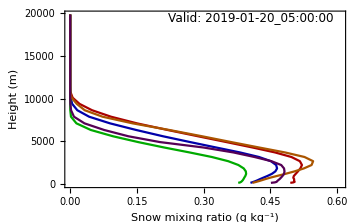

```mathematica
z5=ListPlot[{typeM2M⟦6⟧⟦6⟧,typeTH⟦6⟧⟦6⟧,typeWDM6⟦6⟧⟦6⟧,typeMILL⟦6⟧⟦6⟧,typeGODD⟦6⟧⟦6⟧},Frame->True,FrameLabel->{listTypes⟦6⟧, "Height (m)"},PlotStyle->{Darker[Blue],Darker[Red],Darker[Green],Darker[Orange],Darker[Purple]},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman") }, Joined->True,GridLines->None
,PlotRange -> {{Automatic,listmaxes⟦6⟧+ 0.2*listmaxes⟦6⟧},{0,Automatic}},ImageSize->Medium,(*PlotLegends->SwatchLegend[{"M2M","THOM","WDM6", "MILL","GODD"}, LegendLabel ->"Microphysics scheme", LegendFunction->"Frame"],*)Epilog->Inset[Style[listTimes⟦6⟧,FontFamily->"Times New Roman",12],{listmaxes⟦6⟧-.1,19500}]]
```

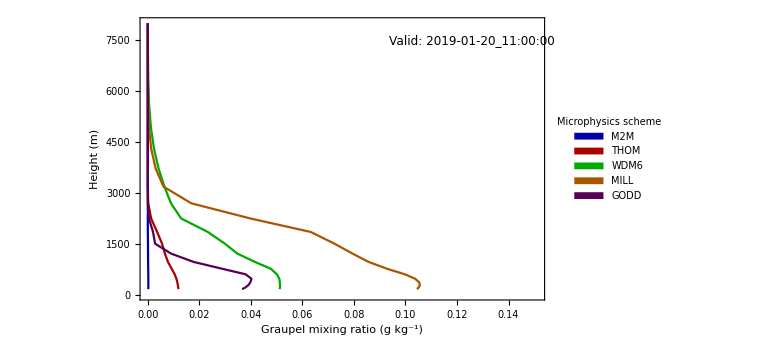

```mathematica
g11=ListPlot[{typeM2M⟦5⟧⟦12⟧,typeTH⟦5⟧⟦12⟧,typeWDM6⟦5⟧⟦12⟧,typeMILL⟦5⟧⟦12⟧,typeGODD⟦5⟧⟦12⟧},Frame->True,FrameLabel->{listTypes⟦5⟧, "Height (m)"},PlotStyle->{Darker[Blue],Darker[Red],Darker[Green],Darker[Orange],Darker[Purple]},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman") }, Joined->True,GridLines->None
,PlotRange -> {{Automatic,listmaxes⟦5⟧+ 0.2*listmaxes⟦5⟧},{0,8000}},ImageSize->Large,PlotLegends->SwatchLegend[{"M2M","THOM","WDM6", "MILL","GODD"}, LegendLabel ->"Microphysics scheme", LegendFunction->"Frame"],Epilog->Inset[Style[listTimes⟦12⟧,FontFamily->"Times New Roman",12],{listmaxes⟦5⟧ - .0002,7500}]]
```

```mathematica
AppendTo[listTypes,"Mixing ratio (g kg^-1)"];
```

```mathematica
g11MILL=ListPlot[{typeMILL⟦5⟧⟦12⟧,typeMILL⟦6⟧⟦12⟧},Frame->True,FrameLabel->{listTypes⟦7⟧, "Height (m)"},PlotStyle->{Darker[Blue],Darker[Red],Darker[Green],Darker[Orange],Darker[Purple]},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman") }, Joined->True,GridLines->None, ImageSize->Large,PlotRange -> {{Automatic, 0.409},{0,8000}},(*PlotLegends->SwatchLegend[{"q_g","q_s"}, LegendLabel ->"Hydrometeor", LegendFunction->"Frame"],*)Epilog->{Inset[Style[listTimes⟦12⟧,FontFamily->"Times New Roman",12],{0.338,7100}],Inset[Style["Millbrandt-Yao",FontFamily->"Times New Roman",12],{0.366,7500}]}];
```

```mathematica
g14MILL=ListPlot[{typeMILL⟦5⟧⟦15⟧,typeMILL⟦6⟧⟦15⟧},Frame->True,FrameLabel->{listTypes⟦7⟧, "Height (m)"},PlotStyle->{Darker[Blue],Darker[Red],Darker[Green],Darker[Orange],Darker[Purple]},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman") }, Joined->True,GridLines->None, ImageSize->Large,PlotRange -> {{Automatic, 0.409},{0,8000}},(*PlotLegends->SwatchLegend[{"q_g","q_s"}, LegendLabel ->"Hydrometeor", LegendFunction->"Frame"],*)Epilog->{Inset[Style[listTimes⟦15⟧,FontFamily->"Times New Roman",12],{0.338,7100}],Inset[Style["Millbrandt-Yao",FontFamily->"Times New Roman",12],{0.366,7500}]}];
```

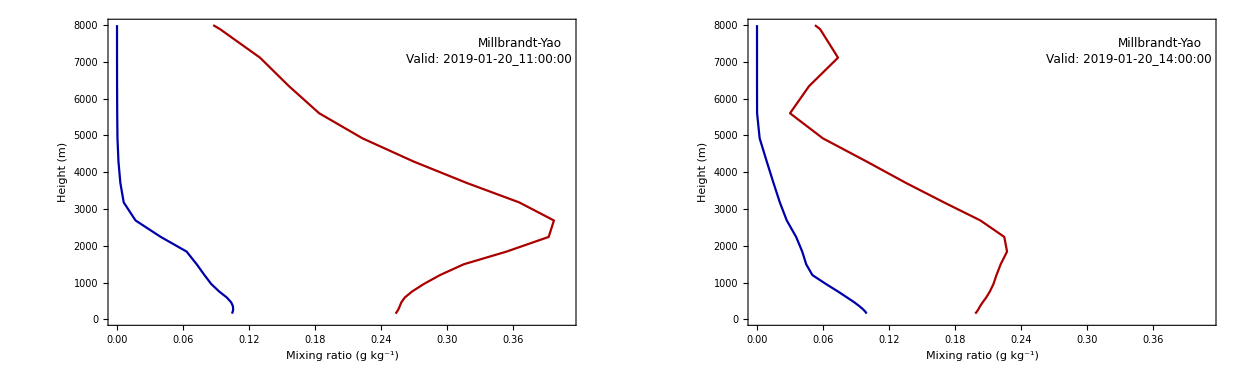

```mathematica
ggrid=GraphicsGrid[{{g11MILL,g14MILL}},Frame->All];
legg=SwatchLegend[{Darker[Blue],Darker[Red],Darker[Green],Darker[Orange],Darker[Purple]},{"Graupel","Snow"}, LegendLabel ->"Hydrometeor", LegendFunction->"Frame"];
mixgridg=Legended[ggrid,Placed[legg,{Right,Right}]]
```

```mathematica
vidMILL=Manipulate[ListPlot[{typeMILL⟦5⟧⟦time⟧,typeMILL⟦6⟧⟦time⟧},Frame->True,FrameLabel->{listTypes⟦7⟧, "Height (m)"},PlotStyle->{Darker[Blue],Darker[Red],Darker[Green],Darker[Orange],Darker[Purple]},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman") }, Joined->True,GridLines->None, ImageSize->Large,PlotRange -> {{Automatic,.409},{0,8000}},PlotLegends->SwatchLegend[{"q_g","q_s"}, LegendLabel ->"Hydrometeor", LegendFunction->"Frame"],Epilog->{Inset[Style[listTimes⟦time⟧,FontFamily->"Times New Roman",12],{0.338,7100}],Inset[Style["Millbrandt-Yao",FontFamily->"Times New Roman",12],{0.366,7500}]}],{time,12,15,1}]
```

Part::partd: Part specification typeMILL⟦5⟧ is longer than depth of object.

Part::partw: Part 12 of typeMILL⟦5⟧ does not exist.

Part::partd: Part specification typeMILL⟦6⟧ is longer than depth of object.

Part::partw: Part 12 of typeMILL⟦6⟧ does not exist.

Part::partd: Part specification listTypes⟦7⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
Export["/Users/Michael/Desktop/vidMILL.mov",vidMILL]
```

/Users/Michael/Desktop/vidMILL.mov

```mathematica
Export["mixgridgMILL.png",mixgridg]
```

mixgridgMILL.png

```mathematica
Export["g11MILL.jpg",g11MILL]
```

g11MILL.jpg

```mathematica
z11=ListPlot[{typeM2M⟦6⟧⟦12⟧,typeTH⟦6⟧⟦12⟧,typeWDM6⟦6⟧⟦12⟧,typeMILL⟦6⟧⟦12⟧,typeGODD⟦6⟧⟦12⟧},Frame->True,FrameLabel->{listTypes⟦6⟧, "Height (m)"},PlotStyle->{Darker[Blue],Darker[Red],Darker[Green],Darker[Orange],Darker[Purple]},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman") }, Joined->True,GridLines->None
,PlotRange -> {{Automatic,listmaxes⟦6⟧+ 0.2*listmaxes⟦6⟧},{0,Automatic}},ImageSize->Medium,(*PlotLegends->SwatchLegend[{"M2M","THOM","WDM6", "MILL","GODD"}, LegendLabel ->"Microphysics scheme", LegendFunction->"Frame"],*)Epilog->Inset[Style[listTimes⟦12⟧,FontFamily->"Times New Roman",12],{listmaxes⟦6⟧-.1,19500}]];
```

```mathematica
z17=ListPlot[{typeM2M⟦6⟧⟦18⟧,typeTH⟦6⟧⟦18⟧,typeWDM6⟦6⟧⟦18⟧,typeMILL⟦6⟧⟦18⟧,typeGODD⟦6⟧⟦18⟧},Frame->True,FrameLabel->{listTypes⟦6⟧, "Height (m)"},PlotStyle->{Darker[Blue],Darker[Red],Darker[Green],Darker[Orange],Darker[Purple]},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman") }, Joined->True,GridLines->None
,PlotRange -> {{Automatic,listmaxes⟦6⟧+ 0.2*listmaxes⟦6⟧},{0,Automatic}},ImageSize->Medium,(*PlotLegends->SwatchLegend[{"M2M","THOM","WDM6", "MILL","GODD"}, LegendLabel ->"Microphysics scheme", LegendFunction->"Frame"],*)Epilog->Inset[Style[listTimes⟦18⟧,FontFamily->"Times New Roman",12],{listmaxes⟦6⟧-.1,19500}]];
```

```mathematica
z23=ListPlot[{typeM2M⟦6⟧⟦24⟧,typeTH⟦6⟧⟦24⟧,typeWDM6⟦6⟧⟦24⟧,typeMILL⟦6⟧⟦24⟧,typeGODD⟦6⟧⟦24⟧},Frame->True,FrameLabel->{listTypes⟦6⟧, "Height (m)"},PlotStyle->{Darker[Blue],Darker[Red],Darker[Green],Darker[Orange],Darker[Purple]},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman") }, Joined->True,GridLines->None
,PlotRange -> {{Automatic,0.02},{0,Automatic}},ImageSize->Medium,(*PlotLegends->SwatchLegend[{"M2M","THOM","WDM6", "MILL","GODD"}, LegendLabel ->"Microphysics scheme", LegendFunction->"Frame"],*)Epilog->Inset[Style[listTimes⟦24⟧,FontFamily->"Times New Roman",12],{listmaxes⟦6⟧-.1,19500}]];
```

```mathematica
mix=GraphicsGrid[{{z5,z11},{z17,z23}},Frame->True];
```

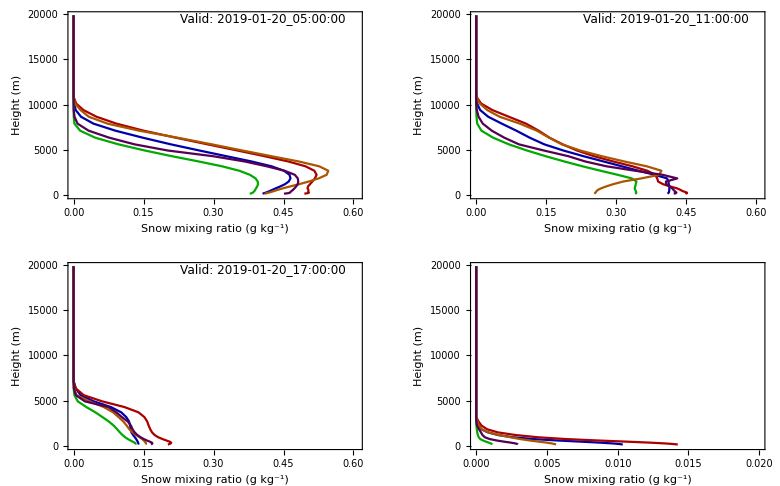

```mathematica
leg=SwatchLegend[{Darker[Blue],Darker[Red],Darker[Green],Darker[Orange],Darker[Purple]},{"M2M","THOM","WDM6", "MILL","GODD"}, LegendLabel ->"Microphysics scheme", LegendFunction->"Frame"];
mixgrid=Legended[mix,Placed[leg,{Right,Right}]]
```

```mathematica
Export["mixgrid.png",mixgrid]
```

mixgrid.png

## Some statistical data

```mathematica
(*same domain as the section just above this one*)
```

#### Morrison 2 moment

```mathematica
seperatetimesM2M=Partition[Flatten[Import["Data_Files/domain_snowmix_dataM2Mtimes.txt","CSV"]],15504];
timesheightsM2M=Table[Partition[seperatetimesM2M⟦i⟧,408],{i,1,24}];
```

```mathematica
meansM2M=Table[Mean[timesheightsM2M⟦Time⟧⟦Height⟧],{Time,1,24},{Height,1,38}];
stdvsM2M = Table[StandardDeviation[timesheightsM2M⟦Time⟧⟦Height⟧],{Time,1,24},{Height,1,38}];
meansandheightsM2M=Prepend[meansM2M,heights];
transmeansandheightsM2M=Transpose[meansandheightsM2M];
DateandTime2 = Table[DateObject[{2019,1,20,i}],{i,00,23}];
labels=Prepend[DateandTime2,"Height (m)"];
transmeansandheightsdaytimeM2M=Prepend[transmeansandheightsM2M,labels];
Grid[transmeansandheightsdaytimeM2M,Frame->All];
```

```mathematica
allatmosdataM2M=Table[Mean[meansM2M⟦time⟧],{time,1,24}];
```

```mathematica
meansloweratmosM2M=Table[Mean[timesheightsM2M⟦Time⟧⟦Height⟧],{Time,1,24},{Height,1,18}];
neworderM2M=Flatten[Table[Append[{},meansloweratmosM2M⟦time⟧⟦height⟧],{height,1,18},{time,1,24}]];
levelsM2M=Partition[neworderM2M,18];
```

```mathematica
M2Mmixratios=Table[Mean[levelsM2M⟦time⟧],{time,1,24}];
```

```mathematica
(*here we take the standard deviation of all valuses for the lower atmosphere for a measure of variability in mixing ratios*)
```

```mathematica
stdvsloweratmosM2M=Table[StandardDeviation[timesheightsM2M⟦Time⟧⟦Height⟧],{Time,1,24},{Height,1,18}];
```

```mathematica
neworderM2Mstdv=Flatten[Table[Append[{},stdvsloweratmosM2M⟦time⟧⟦height⟧],{height,1,18},{time,1,24}]];
stdvlevelsM2M=Partition[neworderM2Mstdv,18];
```

```mathematica
M2Mmixratiosstdv=Table[Mean[stdvlevelsM2M⟦time⟧],{time,1,24}];
```

```mathematica
lowerAtmosplotM2M=DateListPlot[M2Mmixratios,{2019,1,20,00},Frame->True,FrameLabel->{"Time", "Average snow mixing ratio (g kg^-1)"},PlotStyle->{Darker[Blue]},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman") }, Joined->True,GridLines->None
,PlotRange -> {{Automatic,Automatic},{0,Automatic}},ImageSize->Large,PlotLegends->SwatchLegend[{"M2M"}, LegendLabel ->"Microphysics scheme", LegendFunction->"Frame"] ];
```

#### Thompson

```mathematica
(*same domain as the section just above this one*)
```

```mathematica
seperatetimesTH=Partition[Flatten[Import["Data_Files/domain_snowmix_dataTHOMtimes.txt","CSV"]],15504];
timesheightsTH=Table[Partition[seperatetimesTH⟦i⟧,408],{i,1,24}];
```

```mathematica
meansTH=Table[Mean[timesheightsTH⟦Time⟧⟦Height⟧],{Time,1,24},{Height,1,38}];
stdvsTH = Table[StandardDeviation[timesheightsTH⟦Time⟧⟦Height⟧],{Time,1,24},{Height,1,38}];
meansandheightsTH=Prepend[meansTH,heights];
transmeansandheightsTH=Transpose[meansandheightsTH];
DateandTime2 = Table[DateObject[{2019,1,20,i}],{i,00,23}];
labels=Prepend[DateandTime2,"Height (m)"];
transmeansandheightsdaytimeTH=Prepend[transmeansandheightsTH,labels];
Grid[transmeansandheightsdaytimeTH,Frame->All];
```

```mathematica
allatmosdataTH=Table[Mean[meansTH⟦time⟧],{time,1,24}];
```

```mathematica
meansloweratmosTH=Table[Mean[timesheightsTH⟦Time⟧⟦Height⟧],{Time,1,24},{Height,1,18}];
neworderTH=Flatten[Table[Append[{},meansloweratmosTH⟦time⟧⟦height⟧],{height,1,18},{time,1,24}]];
levelsTH=Partition[neworderTH,18];
```

```mathematica
THmixratios=Table[Mean[levelsTH⟦time⟧],{time,1,24}];
```

```mathematica
(*here we take the standard deviation of all valuses for the lower atmosphere for a measure of variability in mixing ratios*)
```

```mathematica
stdvsloweratmosTH=Table[StandardDeviation[timesheightsTH⟦Time⟧⟦Height⟧],{Time,1,24},{Height,1,18}];
```

```mathematica
neworderTHstdv=Flatten[Table[Append[{},stdvsloweratmosTH⟦time⟧⟦height⟧],{height,1,18},{time,1,24}]];
stdvlevelsTH=Partition[neworderTHstdv,18];
```

```mathematica
THmixratiosstdv=Table[Mean[stdvlevelsTH⟦time⟧],{time,1,24}];
```

```mathematica
lowerAtmosplotTH=DateListPlot[THmixratios,{2019,1,20,00},Frame->True,FrameLabel->{"Time", "Average snow mixing ratio (g kg^-1)"},PlotStyle->{Darker[Red]},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman") }, Joined->True,GridLines->None
,PlotRange -> {{Automatic,Automatic},{0,Automatic}},ImageSize->Large,PlotLegends->SwatchLegend[{"THOM"}, LegendLabel ->"Microphysics scheme", LegendFunction->"Frame"] ];
```

### WDM6

```mathematica
seperatetimesWDM6=Partition[Flatten[Import["Data_Files/domain_snowmix_dataWDM6times.txt","CSV"]],15504];
timesheightsWDM6=Table[Partition[seperatetimesWDM6⟦i⟧,408],{i,1,24}];
```

```mathematica
meansWDM6=Table[Mean[timesheightsWDM6⟦Time⟧⟦Height⟧],{Time,1,24},{Height,1,38}];
stdvsWDM6 = Table[StandardDeviation[timesheightsWDM6⟦Time⟧⟦Height⟧],{Time,1,24},{Height,1,38}];
meansandheightsWDM6=Prepend[meansWDM6,heights];
transmeansandheightsWDM6=Transpose[meansandheightsWDM6];
DateandTime2 = Table[DateObject[{2019,1,20,i}],{i,00,23}];
labels=Prepend[DateandTime2,"Height (m)"];
transmeansandheightsdaytimeWDM6=Prepend[transmeansandheightsWDM6,labels];
Grid[transmeansandheightsdaytimeWDM6,Frame->All];
```

```mathematica
allatmosdataWDM6=Table[Mean[meansWDM6⟦time⟧],{time,1,24}];
```

```mathematica
meansloweratmosWDM6=Table[Mean[timesheightsWDM6⟦Time⟧⟦Height⟧],{Time,1,24},{Height,1,18}];
neworderWDM6=Flatten[Table[Append[{},meansloweratmosWDM6⟦time⟧⟦height⟧],{height,1,18},{time,1,24}]];
levelsWDM6=Partition[neworderWDM6,18];
```

```mathematica
WDM6mixratios=Table[Mean[levelsWDM6⟦time⟧],{time,1,24}];
```

```mathematica
(*here we take the standard deviation of all valuses for the lower atmosphere for a measure of variability in mixing ratios*)
```

```mathematica
stdvsloweratmosWDM6=Table[StandardDeviation[timesheightsWDM6⟦Time⟧⟦Height⟧],{Time,1,24},{Height,1,18}];
```

```mathematica
neworderWDM6stdv=Flatten[Table[Append[{},stdvsloweratmosWDM6⟦time⟧⟦height⟧],{height,1,18},{time,1,24}]];
stdvlevelsWDM6=Partition[neworderWDM6stdv,18];
```

```mathematica
WDM6mixratiosstdv=Table[Mean[stdvlevelsWDM6⟦time⟧],{time,1,24}];
```

```mathematica
lowerAtmosplotWDM6=DateListPlot[WDM6mixratios,{2019,1,20,00},Frame->True,FrameLabel->{"Time", "Average snow mixing ratio (g kg^-1)"},PlotStyle->{Darker[Green]},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman") }, Joined->True,GridLines->None
,PlotRange -> {{Automatic,Automatic},{0,Automatic}},ImageSize->Large,PlotLegends->SwatchLegend[{"WDM6"}, LegendLabel ->"Microphysics scheme", LegendFunction->"Frame"] ];
```

#### Millbrandt

```mathematica
seperatetimesMILL=Partition[Flatten[Import["Data_Files/domain_snowmix_dataMILLtimes.txt","CSV"]],15504];
timesheightsMILL=Table[Partition[seperatetimesMILL⟦i⟧,408],{i,1,24}];
```

```mathematica
meansMILL=Table[Mean[timesheightsMILL⟦Time⟧⟦Height⟧],{Time,1,24},{Height,1,38}];
stdvsMILL = Table[StandardDeviation[timesheightsMILL⟦Time⟧⟦Height⟧],{Time,1,24},{Height,1,38}];
meansandheightsMILL=Prepend[meansMILL,heights];
transmeansandheightsMILL=Transpose[meansandheightsMILL];
DateandTime2 = Table[DateObject[{2019,1,20,i}],{i,00,23}];
labels=Prepend[DateandTime2,"Height (m)"];
transmeansandheightsdaytimeMILL=Prepend[transmeansandheightsMILL,labels];
Grid[transmeansandheightsdaytimeMILL,Frame->All];
```

```mathematica
allatmosdataMILL=Table[Mean[meansMILL⟦time⟧],{time,1,24}];
```

```mathematica
meansloweratmosMILL=Table[Mean[timesheightsMILL⟦Time⟧⟦Height⟧],{Time,1,24},{Height,1,18}];
neworderMILL=Flatten[Table[Append[{},meansloweratmosMILL⟦time⟧⟦height⟧],{height,1,18},{time,1,24}]];
levelsMILL=Partition[neworderMILL,18];
```

```mathematica
MILLmixratios=Table[Mean[levelsMILL⟦time⟧],{time,1,24}];
```

```mathematica
(*here we take the standard deviation of all valuses for the lower atmosphere for a measure of variability in mixing ratios*)
```

```mathematica
stdvsloweratmosMILL=Table[StandardDeviation[timesheightsMILL⟦Time⟧⟦Height⟧],{Time,1,24},{Height,1,18}];
```

```mathematica
neworderMILLstdv=Flatten[Table[Append[{},stdvsloweratmosMILL⟦time⟧⟦height⟧],{height,1,18},{time,1,24}]];
stdvlevelsMILL=Partition[neworderMILLstdv,18];
```

```mathematica
MILLmixratiosstdv=Table[Mean[stdvlevelsMILL⟦time⟧],{time,1,24}];
```

```mathematica
lowerAtmosplotMILL=DateListPlot[MILLmixratios,{2019,1,20,00},Frame->True,FrameLabel->{"Time", "Average snow mixing ratio (g kg^-1)"},PlotStyle->{Darker[Orange]},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman") }, Joined->True,GridLines->None
,PlotRange -> {{Automatic,Automatic},{0,Automatic}},ImageSize->Large,PlotLegends->SwatchLegend[{"MILL"}, LegendLabel ->"Microphysics scheme", LegendFunction->"Frame"] ];
```

#### Goddard

```mathematica
seperatetimesGODD=Partition[Flatten[Import["Data_Files/domain_snowmix_dataGODDtimes.txt","CSV"]],15504];
timesheightsGODD=Table[Partition[seperatetimesGODD⟦i⟧,408],{i,1,24}];
```

```mathematica
meansGODD=Table[Mean[timesheightsGODD⟦Time⟧⟦Height⟧],{Time,1,24},{Height,1,38}];
stdvsGODD = Table[StandardDeviation[timesheightsGODD⟦Time⟧⟦Height⟧],{Time,1,24},{Height,1,38}];
meansandheightsGODD=Prepend[meansGODD,heights];
transmeansandheightsGODD=Transpose[meansandheightsGODD];
DateandTime2 = Table[DateObject[{2019,1,20,i}],{i,00,23}];
labels=Prepend[DateandTime2,"Height (m)"];
transmeansandheightsdaytimeGODD=Prepend[transmeansandheightsGODD,labels];
Grid[transmeansandheightsdaytimeGODD,Frame->All];
```

```mathematica
allatmosdataGODD=Table[Mean[meansGODD⟦time⟧],{time,1,24}];
```

```mathematica
(*This plot includes all levels of the atmosphere , not just < 5000 m, as we see below*)
```

```mathematica
allAtmosplotGODD=DateListPlot[allatmosdataGODD,{2019,1,20,00},Frame->True,FrameLabel->{"Time", "Average snow mixing ratio (g kg^-1)"},PlotStyle->{Darker[Purple]},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman") }, Joined->True,GridLines->None
,PlotRange -> {{Automatic,Automatic},{0,Automatic}},ImageSize->Large,PlotLegends->SwatchLegend[{"GODD"}, LegendLabel ->"Microphysics scheme", LegendFunction->"Frame"] ];
```

```mathematica
meansloweratmosGODD=Table[Mean[timesheightsGODD⟦Time⟧⟦Height⟧],{Time,1,24},{Height,1,18}];
neworderGODD=Flatten[Table[Append[{},meansloweratmosGODD⟦time⟧⟦height⟧],{height,1,18},{time,1,24}]];
levelsGODD=Partition[neworderGODD,18];
GODDmixratios=Table[Mean[levelsGODD⟦time⟧],{time,1,24}];
```

```mathematica
(*here we take the standard deviation of all valuses for the lower atmosphere for a measure of variability in mixing ratios*)
```

```mathematica
stdvsloweratmosGODD=Table[StandardDeviation[timesheightsGODD⟦Time⟧⟦Height⟧],{Time,1,24},{Height,1,18}];
```

```mathematica
neworderGODDstdv=Flatten[Table[Append[{},stdvsloweratmosGODD⟦time⟧⟦height⟧],{height,1,18},{time,1,24}]];
stdvlevelsGODD=Partition[neworderGODDstdv,18];
```

```mathematica
GODDmixratiosstdv=Table[Mean[stdvlevelsGODD⟦time⟧],{time,1,24}];
```

```mathematica
lowerAtmosplotGODD=DateListPlot[GODDmixratios,{2019,1,20,00},Frame->True,FrameLabel->{"Time", "Average snow mixing ratio (g kg^-1)"},PlotStyle->{Darker[Purple]},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman") }, Joined->True,GridLines->None
,PlotRange -> {{Automatic,Automatic},{0,Automatic}},ImageSize->Large,PlotLegends->SwatchLegend[{"GODD"}, LegendLabel ->"Microphysics scheme", LegendFunction->"Frame"] ];
```

```mathematica
(*Note that this plot is just for the lower atmosphere < ~5600 m , 500 mb in the atmosphere *)
```

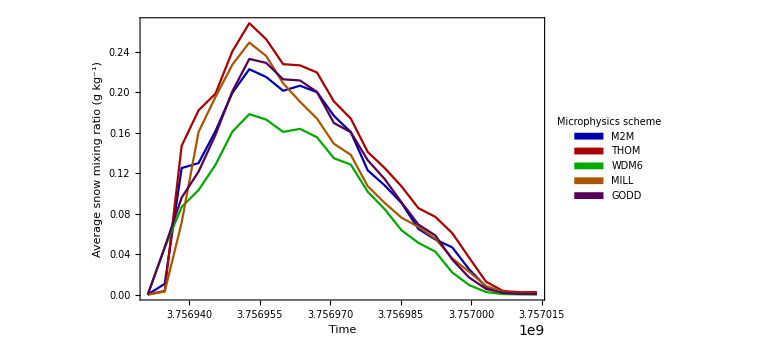

```mathematica
AllAtmospherePlot=DateListPlot[{allatmosdataM2M,allatmosdataTH,allatmosdataWDM6, allatmosdataMILL,allatmosdataGODD},{2019,1,20,00},Frame->True,FrameLabel->{"Time", "Average snow mixing ratio (g kg^-1)"},PlotStyle->{Darker[Blue],Darker[Red],Darker[Green],Darker[Orange],Darker[Purple]},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman") }, Joined->True,GridLines->None
,PlotRange -> {{Automatic,Automatic},{0,Automatic}},ImageSize->Large,PlotLegends->SwatchLegend[{"M2M","THOM","WDM6", "MILL","GODD"}, LegendLabel ->"Microphysics scheme", LegendFunction->"Frame"] ]
```

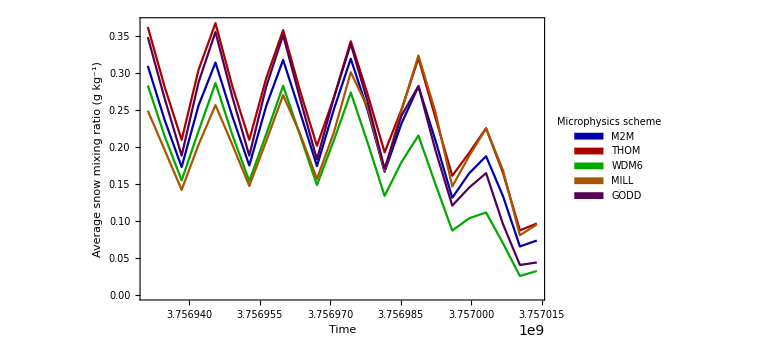

```mathematica
LowerAtmospherePlot=DateListPlot[{M2Mmixratios,THmixratios,WDM6mixratios, MILLmixratios,GODDmixratios},{2019,1,20,00},Frame->True,FrameLabel->{"Time", "Average snow mixing ratio (g kg^-1)"},PlotStyle->{Darker[Blue],Darker[Red],Darker[Green],Darker[Orange],Darker[Purple]},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman") }, Joined->True,GridLines->None
,PlotRange -> {{Automatic,Automatic},{0,Automatic}},ImageSize->Large,PlotLegends->SwatchLegend[{"M2M","THOM","WDM6", "MILL","GODD"}, LegendLabel ->"Microphysics scheme", LegendFunction->"Frame"] ]
```

```mathematica
Grid[{{LowerAtmospherePlot,avgAccumsnowplot,AllAtmospherePlot}}]
```

-Graphics- | -Graphics- | -Graphics-

```mathematica
(*Interesting things to look at are WDM6. Why does it predict more snowfall than MILL, when snow mixing ratios are relatively similar, especially during the early parts of the storm. Could it have to do whith what variables get predicted. Potentially MILL significantly underpredicts Qs because it tries to compensate by trying to have a greater Ns - however it fails to have a large enough Ns.*)
```

```mathematica
Import["/Users/Michael/Desktop/Screen Shot 2020-11-08 at 11.23.00 AM.png"]
```

-Graphics-

## Tempeatures

```mathematica
GODDT2midd=Partition[Flatten[Import["midd_T2_dataGODD.txt", "CSV"]],49];
meanGODDT2midd=Mean[GODDT2midd- 273.15]; (*Subtract 273.15 to convert to degrees celcius*)
GODDT2times = Transpose[{DateandTime, meanGODDT2midd}];
THOMT2midd=Partition[Flatten[Import["midd_T2_dataTHOM.txt", "CSV"]],49];
meanTHOMT2midd=Mean[THOMT2midd - 273.15];
THOMT2times = Transpose[{DateandTime, meanTHOMT2midd}];
WDM6T2midd=Partition[Flatten[Import["midd_T2_dataWDM6.txt", "CSV"]],49];
meanWDM6T2midd=Mean[WDM6T2midd- 273.15];
WDM6T2times = Transpose[{DateandTime, meanWDM6T2midd}];
M2MT2midd=Partition[Flatten[Import["midd_T2_dataM2M.txt", "CSV"]],49];
meanM2MT2midd=Mean[M2MT2midd- 273.15];
M2MT2times = Transpose[{DateandTime, meanM2MT2midd}];
MILLT2midd=Partition[Flatten[Import["midd_T2_dataMILL.txt", "CSV"]],49];
meanMILLT2midd=Mean[MILLT2midd- 273.15];
MILLT2times = Transpose[{DateandTime, meanMILLT2midd}];
```

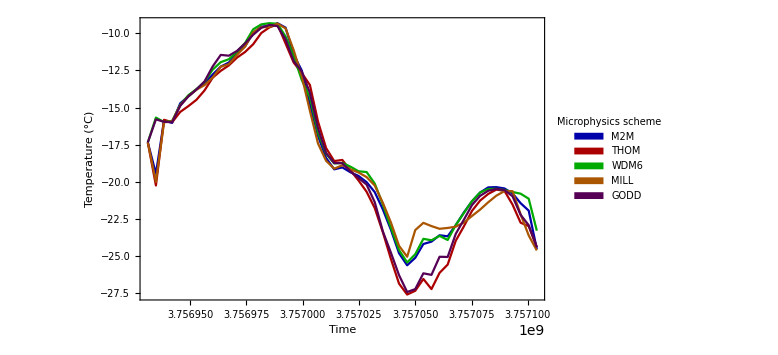

```mathematica
T2plot=DateListPlot[{meanM2MT2midd,meanTHOMT2midd,meanWDM6T2midd, meanMILLT2midd,meanGODDT2midd},{2019,1,20,00},Frame->True,FrameLabel->{"Time", "Temperature (°C)"},PlotStyle->{Darker[Blue],Darker[Red],Darker[Green],Darker[Orange],Darker[Purple]},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman") }, Joined->True,GridLines->None
,PlotRange -> {{Automatic,Automatic},{0,Automatic}},ImageSize->Large,PlotLegends->SwatchLegend[{"M2M","THOM","WDM6", "MILL","GODD"}, LegendLabel ->"Microphysics scheme", LegendFunction->"Frame"] ]
```

## Reflectivity

```mathematica
seperatetimesdbzTH=Partition[Flatten[Import["Data_Files/dbz_dataTHOM.txt","CSV"]],15504];
timesheightsdbzTH=Table[Partition[seperatetimesdbzTH⟦i⟧,408],{i,1,24}];
meansdbzTH=Table[Mean[timesheightsdbzTH⟦Time⟧⟦Height⟧],{Time,1,24},{Height,1,38}];
meansheightsdbzTH=Table[Transpose[{{meansdbzTH⟦Time⟧⟦Height⟧},{heights⟦Height⟧}}],{Time,1,24},{Height,1,38}];
timespartitionTH=Partition[Flatten[meansheightsdbzTH],76];
reflectivityTH=Table[Partition[timespartitionTH⟦time⟧,2],{time,1,24}];
```

```mathematica
seperatetimesdbzM2M=Partition[Flatten[Import["Data_Files/dbz_dataM2M.txt","CSV"]],15504];
timesheightsdbzM2M=Table[Partition[seperatetimesdbzM2M⟦i⟧,408],{i,1,24}];
meansdbzM2M=Table[Mean[timesheightsdbzM2M⟦Time⟧⟦Height⟧],{Time,1,24},{Height,1,38}];
meansheightsdbzM2M=Table[Transpose[{{meansdbzM2M⟦Time⟧⟦Height⟧},{heights⟦Height⟧}}],{Time,1,24},{Height,1,38}];
timespartitionM2M=Partition[Flatten[meansheightsdbzM2M],76];
reflectivityM2M=Table[Partition[timespartitionM2M⟦time⟧,2],{time,1,24}];
```

```mathematica
seperatetimesdbzWDM6=Partition[Flatten[Import["Data_Files/dbz_dataWDM6.txt","CSV"]],15504];
timesheightsdbzWDM6=Table[Partition[seperatetimesdbzWDM6⟦i⟧,408],{i,1,24}];
meansdbzWDM6=Table[Mean[timesheightsdbzWDM6⟦Time⟧⟦Height⟧],{Time,1,24},{Height,1,38}];
meansheightsdbzWDM6=Table[Transpose[{{meansdbzWDM6⟦Time⟧⟦Height⟧},{heights⟦Height⟧}}],{Time,1,24},{Height,1,38}];
timespartitionWDM6=Partition[Flatten[meansheightsdbzWDM6],76];
reflectivityWDM6=Table[Partition[timespartitionWDM6⟦time⟧,2],{time,1,24}];
```

```mathematica
seperatetimesdbzMILL=Partition[Flatten[Import["Data_Files/dbz_dataMILL.txt","CSV"]],15504];
timesheightsdbzMILL=Table[Partition[seperatetimesdbzMILL⟦i⟧,408],{i,1,24}];
meansdbzMILL=Table[Mean[timesheightsdbzMILL⟦Time⟧⟦Height⟧],{Time,1,24},{Height,1,38}];
meansheightsdbzMILL=Table[Transpose[{{meansdbzMILL⟦Time⟧⟦Height⟧},{heights⟦Height⟧}}],{Time,1,24},{Height,1,38}];
timespartitionMILL=Partition[Flatten[meansheightsdbzMILL],76];
reflectivityMILL=Table[Partition[timespartitionMILL⟦time⟧,2],{time,1,24}];
```

```mathematica
seperatetimesdbzGODD=Partition[Flatten[Import["Data_Files/dbz_dataGODD.txt","CSV"]],15504];
timesheightsdbzGODD=Table[Partition[seperatetimesdbzGODD⟦i⟧,408],{i,1,24}];
meansdbzGODD=Table[Mean[timesheightsdbzGODD⟦Time⟧⟦Height⟧],{Time,1,24},{Height,1,38}];
meansheightsdbzGODD=Table[Transpose[{{meansdbzGODD⟦Time⟧⟦Height⟧},{heights⟦Height⟧}}],{Time,1,24},{Height,1,38}];
timespartitionGODD=Partition[Flatten[meansheightsdbzGODD],76];
reflectivityGODD=Table[Partition[timespartitionGODD⟦time⟧,2],{time,1,24}];
```

```mathematica
maxdbz=Max[{seperatetimesdbzGODD,seperatetimesM2M,seperatetimesTH,seperatetimesWDM6,seperatetimesdbzMILL}];
```

```mathematica
radar=Manipulate[ListPlot[{reflectivityM2M⟦time⟧,reflectivityTH⟦time⟧,reflectivityWDM6⟦time⟧,reflectivityMILL⟦time⟧,reflectivityGODD⟦time⟧},Frame->True,FrameLabel->{"Simulated Equivalent Radar Reflectivity Factor (dBZ)", "Height (m)"},PlotStyle->{Darker[Blue],Darker[Red],Darker[Green],Darker[Orange],Darker[Purple]},PlotStyle->Thickness[.003],LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman") }, Joined->True,GridLines->None,PlotRange -> {{Automatic,maxdbz - 2.0},{0,Automatic}},ImageSize->Large,PlotLegends->SwatchLegend[{"M2M","THOM","WDM6", "MILL","GODD"}, LegendLabel ->"Microphysics scheme", LegendFunction->"Frame"] , Epilog->Style[Inset[listTimes⟦2⟧,{maxdbz-12,19500}],FontFamily->"Times New Roman",12]],{time,2,24,1}] (*How to get colors to match reflectivity*)
```

Part::partd: Part specification reflectivityM2M⟦2⟧ is longer than depth of object.

Part::partd: Part specification reflectivityTH⟦2⟧ is longer than depth of object.

Part::partd: Part specification reflectivityWDM6⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

System`ListPlotsDump`messageshead$7676::prng: Value of option PlotRange -> {{Automatic,-2.+maxdbz},{0,Automatic}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

```mathematica
Export["/Users/Michael/Desktop/radar.mov",radar]
```

/Users/Michael/Desktop/radar.mov

```mathematica
time18=ListPlot[{reflectivityM2M⟦18⟧,reflectivityTH⟦18⟧,reflectivityWDM6⟦18⟧,reflectivityMILL⟦18⟧,reflectivityGODD⟦18⟧},Frame->True,FrameLabel->{"Simulated Equivalent Radar Reflectivity Factor (dBZ)", "Height (m)"},PlotStyle->{Darker[Blue],Darker[Red],Darker[Green],Darker[Orange],Darker[Purple]},PlotStyle->Thickness[.003],LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman") }, Joined->True,GridLines->None,PlotRange -> {{Automatic,maxdbz - 2.0},{0,Automatic}},ImageSize->Large,PlotLegends->SwatchLegend[{"M2M","THOM","WDM6", "MILL","GODD"}, LegendLabel ->"Microphysics scheme", LegendFunction->"Frame"] , Epilog->Style[Inset[listTimes⟦2⟧,{maxdbz-12,19500}],FontFamily->"Times New Roman",12]];
```

```mathematica
Export["reflectivity.png",time18]
```

reflectivity.png

## Snow cross section

```mathematica
heights
```

{158.738,210.298,275.99,359.471,464.922,596.802,760.18,961.278,1206.26,1499.59,1844.77,2242.88,2690.3,3181.31,3714.82,4294.53,4923.7,5604.51,6340.67,7115.5,7891.48,8649.78,9389.21,10109.5,10814.1,11510.3,12206.6,12907.,13610.8,14316.3,15020.8,15722.3,16419.8,17113.1,17802.,18486.7,19167.9,19846.4}

```mathematica
verticle=Range[0,20000,200];
```

```mathematica
qscrossTHtimes=Flatten[Import["Data_Files/vert_cross_qs_THOM.txt","CSV"]];
realnumbsTH=Replace[qscrossTHtimes,9.96921*10^36->0,{1}];
realnumbsTHunits=realnumbsTH*1000;
maxplotTH=Max[realnumbsTHunits]
crosstimesTH=Partition[realnumbsTHunits,1800];
crossheightstimesTH=Table[Partition[crosstimesTH⟦time⟧,18],{time,1,24}];
crlongsTH=Table[Transpose[{crossheightstimesTH⟦time⟧⟦height⟧,Range[-73.42813,-71.29266,0.125613]}],{time,1,24},{height,1,100}];
crlongsheightsTH=Table[Insert[crlongsTH⟦time⟧⟦height⟧⟦long⟧,verticle⟦height⟧,2],{time,1,24},{height,1,100},{long,1,18}];
crlongsheightsTHorder=Table[Reverse[crlongsheightsTH⟦time⟧⟦height⟧⟦long⟧],{time,1,24},{height,1,100},{long,1,18}];
flattenorderTH=Partition[Flatten[crlongsheightsTHorder],5400];
forcrossTH=Table[Partition[flattenorderTH⟦time⟧,3],{time,1,24}];
```

0.948249

```mathematica
qscrossM2Mtimes=Flatten[Import["Data_Files/vert_cross_qs_M2M.txt","CSV"]];
realnumbsM2M=Replace[qscrossM2Mtimes,9.96921*10^36->0,{1}];
realnumbsM2Munits=realnumbsM2M*1000;
maxplotM2M=Max[realnumbsM2Munits]
crosstimesM2M=Partition[realnumbsM2Munits,1800];
crossheightstimesM2M=Table[Partition[crosstimesM2M⟦time⟧,18],{time,1,24}];
crlongsM2M=Table[Transpose[{crossheightstimesM2M⟦time⟧⟦height⟧,Range[-73.42813,-71.29266,0.125613]}],{time,1,24},{height,1,100}];
crlongsheightsM2M=Table[Insert[crlongsM2M⟦time⟧⟦height⟧⟦long⟧,verticle⟦height⟧,2],{time,1,24},{height,1,100},{long,1,18}];
crlongsheightsM2Morder=Table[Reverse[crlongsheightsM2M⟦time⟧⟦height⟧⟦long⟧],{time,1,24},{height,1,100},{long,1,18}];
flattenorderM2M=Partition[Flatten[crlongsheightsM2Morder],5400];
forcrossM2M=Table[Partition[flattenorderM2M⟦time⟧,3],{time,1,24}];
```

1.09811

```mathematica
qscrossWDM6times=Flatten[Import["Data_Files/vert_cross_qs_WDM6.txt","CSV"]];
realnumbsWDM6=Replace[qscrossWDM6times,9.96921*10^36->0,{1}];
realnumbsWDM6units=realnumbsWDM6*1000;
maxplotWDM6=Max[realnumbsWDM6units]
crosstimesWDM6=Partition[realnumbsWDM6units,1800];
crossheightstimesWDM6=Table[Partition[crosstimesWDM6⟦time⟧,18],{time,1,24}];
crlongsWDM6=Table[Transpose[{crossheightstimesWDM6⟦time⟧⟦height⟧,Range[-73.42813,-71.29266,0.125613]}],{time,1,24},{height,1,100}];
crlongsheightsWDM6=Table[Insert[crlongsWDM6⟦time⟧⟦height⟧⟦long⟧,verticle⟦height⟧,2],{time,1,24},{height,1,100},{long,1,18}];
crlongsheightsWDM6order=Table[Reverse[crlongsheightsWDM6⟦time⟧⟦height⟧⟦long⟧],{time,1,24},{height,1,100},{long,1,18}];
flattenorderWDM6=Partition[Flatten[crlongsheightsWDM6order],5400];
forcrossWDM6=Table[Partition[flattenorderWDM6⟦time⟧,3],{time,1,24}];
```

0.725293

```mathematica
qscrossMILLtimes=Flatten[Import["Data_Files/vert_cross_qs_MILL.txt","CSV"]];
realnumbsMILL=Replace[qscrossMILLtimes,9.96921*10^36->0,{1}];
realnumbsMILLunits=realnumbsMILL*1000;
maxplotMILL=Max[realnumbsMILLunits]
crosstimesMILL=Partition[realnumbsMILLunits,1800];
crossheightstimesMILL=Table[Partition[crosstimesMILL⟦time⟧,18],{time,1,24}];
crlongsMILL=Table[Transpose[{crossheightstimesMILL⟦time⟧⟦height⟧,Range[-73.42813,-71.29266,0.125613]}],{time,1,24},{height,1,100}];
crlongsheightsMILL=Table[Insert[crlongsMILL⟦time⟧⟦height⟧⟦long⟧,verticle⟦height⟧,2],{time,1,24},{height,1,100},{long,1,18}];
crlongsheightsMILLorder=Table[Reverse[crlongsheightsMILL⟦time⟧⟦height⟧⟦long⟧],{time,1,24},{height,1,100},{long,1,18}];
flattenorderMILL=Partition[Flatten[crlongsheightsMILLorder],5400];
forcrossMILL=Table[Partition[flattenorderMILL⟦time⟧,3],{time,1,24}];
```

0.904589

```mathematica
Length[Range[-73.42813,-71.29266,0.125613]]
```

18

```mathematica
qscrossGODDtimes=Flatten[Import["Data_Files/vert_cross_qs_GODD.txt","CSV"]];
realnumbsGODD=Replace[qscrossGODDtimes,9.96921*10^36->0,{1}];
realnumbsGODDunits=realnumbsGODD*1000;
maxplotGODD=Max[realnumbsGODDunits]
crosstimesGODD=Partition[realnumbsGODDunits,1800];
crossheightstimesGODD=Table[Partition[crosstimesGODD⟦time⟧,18],{time,1,24}];
crlongsGODD=Table[Transpose[{crossheightstimesGODD⟦time⟧⟦height⟧,Range[-73.42813,-71.29265,.125613]}],{time,1,24},{height,1,100}];
crlongsheightsGODD=Table[Insert[crlongsGODD⟦time⟧⟦height⟧⟦long⟧,verticle⟦height⟧,2],{time,1,24},{height,1,100},{long,1,18}];
crlongsheightsGODDorder=Table[Reverse[crlongsheightsGODD⟦time⟧⟦height⟧⟦long⟧],{time,1,24},{height,1,100},{long,1,18}];
flattenorderGODD=Partition[Flatten[crlongsheightsGODDorder],5400];
forcrossGODD=Table[Partition[flattenorderGODD⟦time⟧,3],{time,1,24}];
```

1.12846

```mathematica
Length[realnumbsGODDunits]
```

43200

```mathematica
crosstimesM2M⟦6⟧;
```

```mathematica
{Mean[crosstimesM2M⟦6⟧], StandardDeviation[crosstimesM2M⟦6⟧]}
```

{0.0448761,0.0624008}

```mathematica
{Mean[crosstimesTH⟦6⟧],StandardDeviation[crosstimesTH⟦6⟧]}
```

{0.0530922,0.0688338}

```mathematica
{Mean[crosstimesMILL⟦6⟧],StandardDeviation[crosstimesWDM6⟦6⟧]}
```

{0.0655126,0.0300096}

```mathematica
{Mean[crosstimesWDM6⟦6⟧],StandardDeviation[crosstimesMILL⟦6⟧]}
```

{0.0141712,0.0871546}

```mathematica
{Mean[crosstimesGODD⟦6⟧],StandardDeviation[crosstimesGODD⟦6⟧]}
```

{0.0254105,0.0424192}

```mathematica
{Mean[crosstimesM2M⟦12⟧], StandardDeviation[crosstimesM2M⟦12⟧]}
```

{0.108695,0.171355}

```mathematica
{Mean[crosstimesTH⟦12⟧],StandardDeviation[crosstimesTH⟦12⟧]}
```

{0.123624,0.182416}

```mathematica
{Mean[crosstimesMILL⟦12⟧],StandardDeviation[crosstimesWDM6⟦12⟧]}
```

{0.112332,0.143086}

```mathematica
{Mean[crosstimesWDM6⟦12⟧],StandardDeviation[crosstimesMILL⟦12⟧]}
```

{0.0749168,0.164945}

```mathematica
{Mean[crosstimesGODD⟦12⟧],StandardDeviation[crosstimesGODD⟦12⟧]}
```

{0.109536,0.202399}

```mathematica
listphys={forcrossM2M,forcrossTH,forcrossWDM6,forcrossMILL,forcrossGODD};
maxplot={maxplotM2M,maxplotTH,maxplotWDM6,maxplotMILL,maxplotGODD};
```

```mathematica
Manipulate[ListDensityPlot[listphys⟦microphysics⟧⟦time⟧, PlotRange->{{-73.42813,-71.29265},All,All},Frame->True,FrameLabel->{"Longitude (°)", "Height (m)"},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman")},GridLines->None, ColorFunction->"Rainbow",PlotRange -> {{All,All},{All,All}},ImageSize->Large,PlotLabel -> microphysicslist⟦microphysics⟧,PlotLegends->Placed[BarLegend[{"Rainbow",{0,Max[maxplot]}},LegendMargins->{{0,0},{10,5}},LegendLabel->"Snow mixing ratio (g kg^-1)",LabelStyle->FontFamily->"Times New Roman"],Right]],{microphysics,1,5,1},{time,2,24,1}]
```

Part::partd: Part specification listphys⟦1⟧ is longer than depth of object.

ListDensityPlot::arrayerr: 1. must be a valid array.

```mathematica
Manipulate[ListDensityPlot[listphys⟦microphysics⟧⟦time⟧, PlotRange->{{-73.42813,-71.29265},All,All},Frame->True,FrameLabel->{"Longitude (°)", "Height (m)"},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman")},GridLines->None, ColorFunction->ColorData[{"SunsetColors","Reverse"}],PlotRange -> {{All,All},{All,All}},ImageSize->Large,PlotLabel -> microphysicslist⟦microphysics⟧,PlotLegends->Placed[BarLegend[{ColorData[{"SunsetColors","Reverse"}],{0,Max[maxplot]}},LegendMargins->{{0,0},{10,5}},LegendLabel->"Snow mixing ratio (g kg^-1)",LabelStyle->FontFamily->"Times New Roman"],Right]],{microphysics,1,5,1},{time,2,24,1}]
```

Part::partd: Part specification listphys⟦1⟧ is longer than depth of object.

ListDensityPlot::arrayerr: 1. must be a valid array.

Part::partd: Part specification listphys⟦1⟧ is longer than depth of object.

ListDensityPlot::arrayerr: 1. must be a valid array.

Part::partd: Part specification listphys⟦1⟧ is longer than depth of object.

ListDensityPlot::arrayerr: 1. must be a valid array.

```mathematica
Manipulate[ListDensityPlot[listphys⟦microphysics⟧⟦time⟧, PlotRange->{{-73.42813,-71.29265},All,All},Frame->True,FrameLabel->{"Longitude (°)", "Height (m)"},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman")},GridLines->None, ColorFunction->ColorData[{"BeachColors","Reverse"}],PlotRange -> {{All,All},{All,All}},ImageSize->Large,PlotLabel -> microphysicslist⟦microphysics⟧,PlotLegends->Placed[BarLegend[{ColorData[{"BeachColors","Reverse"}],{0,Max[maxplot]}},LegendMargins->{{0,0},{10,5}},LegendLabel->"Snow mixing ratio (g kg^-1)",LabelStyle->FontFamily->"Times New Roman"],Right]],{microphysics,1,5,1},{time,2,24,1}]
```

Part::partd: Part specification listphys⟦1⟧ is longer than depth of object.

ListDensityPlot::arrayerr: 1. must be a valid array.

Part::partd: Part specification listphys⟦1⟧ is longer than depth of object.

ListDensityPlot::arrayerr: 1. must be a valid array.

Part::partd: Part specification listphys⟦1⟧ is longer than depth of object.

ListDensityPlot::arrayerr: 1. must be a valid array.

```mathematica
crossgrid=Grid[{{Manipulate[ListDensityPlot[listphys⟦1⟧⟦time⟧, PlotRange->{All,All, All},Frame->True,FrameLabel->{"Longitude (°)", "Height (m)"},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman")},GridLines->None, ColorFunction->"Rainbow",PlotRange -> {{All,All},{All,All}},ImageSize->250,PlotLabel -> microphysicslist⟦1⟧,PlotLegends->Placed[BarLegend[{"Rainbow",{0,Max[maxplot]}},LegendMargins->{{0,0},{10,5}},LegendLabel->"Snow mixing ratio (g kg^-1)",LabelStyle->FontFamily->"Times New Roman"],Right]],{time,2,24,1}],Manipulate[ListDensityPlot[listphys⟦2⟧⟦time⟧, PlotRange->{All,All, All},Frame->True,FrameLabel->{"Longitude (°)", "Height (m)"},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman")},GridLines->None, ColorFunction->"Rainbow",PlotRange -> {{All,All},{All,All}},ImageSize->250,PlotLabel -> microphysicslist⟦2⟧,PlotLegends->Placed[BarLegend[{"Rainbow",{0,Max[maxplot]}},LegendMargins->{{0,0},{10,5}},LegendLabel->"Snow mixing ratio (g kg^-1)",LabelStyle->FontFamily->"Times New Roman"],Right]],{time,2,24,1}],Manipulate[ListDensityPlot[listphys⟦3⟧⟦time⟧, PlotRange->{All,All, All},Frame->True,FrameLabel->{"Longitude (°)", "Height (m)"},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman")},GridLines->None, ColorFunction->"Rainbow",PlotRange -> {{All,All},{All,All}},ImageSize->250,PlotLabel -> microphysicslist⟦3⟧,PlotLegends->Placed[BarLegend[{"Rainbow",{0,Max[maxplot]}},LegendMargins->{{0,0},{10,5}},LegendLabel->"Snow mixing ratio (g kg^-1)",LabelStyle->FontFamily->"Times New Roman"],Right]],{time,2,24,1}]},{Manipulate[ListDensityPlot[listphys⟦4⟧⟦time⟧, PlotRange->{All,All, All},Frame->True,FrameLabel->{"Longitude (°)", "Height (m)"},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman")},GridLines->None, ColorFunction->"Rainbow",PlotRange -> {{All,All},{All,All}},ImageSize->250,PlotLabel -> microphysicslist⟦4⟧,PlotLegends->Placed[BarLegend[{"Rainbow",{0,Max[maxplot]}},LegendMargins->{{0,0},{10,5}},LegendLabel->"Snow mixing ratio (g kg^-1)",LabelStyle->FontFamily->"Times New Roman"],Right]],{time,2,24,1}],Manipulate[ListDensityPlot[listphys⟦5⟧⟦time⟧, PlotRange->{All,All, All},Frame->True,FrameLabel->{"Longitude (°)", "Height (m)"},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman")},GridLines->None, ColorFunction->"Rainbow",PlotRange -> {{All,All},{All,All}},ImageSize->250,PlotLabel -> microphysicslist⟦5⟧,PlotLegends->Placed[BarLegend[{"Rainbow",{0,Max[maxplot]}},LegendMargins->{{0,0},{10,5}},LegendLabel->"Snow mixing ratio (g kg^-1)",LabelStyle->FontFamily->"Times New Roman"],Right]],{time,2,24,1}]}}]
```

|  | 
 |  |

Part::partd: Part specification listphys⟦1⟧ is longer than depth of object.

ListDensityPlot::arrayerr: 1. must be a valid array.

Part::partd: Part specification listphys⟦2⟧ is longer than depth of object.

ListDensityPlot::arrayerr: 2. must be a valid array.

Part::partd: Part specification listphys⟦3⟧ is longer than depth of object.

ListDensityPlot::arrayerr: 3. must be a valid array.

Part::partd: Part specification listphys⟦4⟧ is longer than depth of object.

ListDensityPlot::arrayerr: 4. must be a valid array.

Part::partd: Part specification listphys⟦5⟧ is longer than depth of object.

ListDensityPlot::arrayerr: 5. must be a valid array.

```mathematica
M2Mcross=Manipulate[ListDensityPlot[listphys⟦1⟧⟦time⟧, PlotRange->{All,All, All},Frame->True,FrameLabel->{"Longitude (°)", "Height (m)"},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman")},GridLines->None, ColorFunction->"Rainbow",PlotRange -> {{All,All},{All,All}},ImageSize->Large,PlotLabel -> microphysicslist⟦1⟧,PlotLegends->Placed[BarLegend[{"Rainbow",{0,Max[maxplot]}},LegendMargins->{{0,0},{10,5}},LegendLabel->"Snow mixing ratio (g kg^-1)",LabelStyle->FontFamily->"Times New Roman"],Right]],{time,2,24,1}]
```

Part::partd: Part specification listphys⟦1⟧ is longer than depth of object.

ListDensityPlot::arrayerr: 1. must be a valid array.

```mathematica
Export["/Users/Michael/Desktop/M2Mcross.mov",M2Mcross]
```

/Users/Michael/Desktop/M2Mcross.mov

```mathematica
THOMcross=Manipulate[ListDensityPlot[listphys⟦2⟧⟦time⟧, PlotRange->{All,All, All},Frame->True,FrameLabel->{"Longitude (°)", "Height (m)"},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman")},GridLines->None, ColorFunction->"Rainbow",PlotRange -> {{All,All},{All,All}},ImageSize->Large,PlotLabel -> microphysicslist⟦2⟧,PlotLegends->Placed[BarLegend[{"Rainbow",{0,Max[maxplot]}},LegendMargins->{{0,0},{10,5}},LegendLabel->"Snow mixing ratio (g kg^-1)",LabelStyle->FontFamily->"Times New Roman"],Right]],{time,2,24,1}]
```

Part::partd: Part specification listphys⟦2⟧ is longer than depth of object.

ListDensityPlot::arrayerr: 2. must be a valid array.

```mathematica
Export["/Users/Michael/Desktop/THOMcross.mov",THOMcross]
```

/Users/Michael/Desktop/THOMcross.mov

```mathematica
WDM6cross=Manipulate[ListDensityPlot[listphys⟦3⟧⟦time⟧, PlotRange->{All,All, All},Frame->True,FrameLabel->{"Longitude (°)", "Height (m)"},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman")},GridLines->None, ColorFunction->"Rainbow",PlotRange -> {{All,All},{All,All}},ImageSize->Large,PlotLabel -> microphysicslist⟦3⟧,PlotLegends->Placed[BarLegend[{"Rainbow",{0,Max[maxplot]}},LegendMargins->{{0,0},{10,5}},LegendLabel->"Snow mixing ratio (g kg^-1)",LabelStyle->FontFamily->"Times New Roman"],Right]],{time,2,24,1}]
```

Part::partd: Part specification listphys⟦3⟧ is longer than depth of object.

ListDensityPlot::arrayerr: 3. must be a valid array.

```mathematica
Export["/Users/Michael/Desktop/WDM6cross.mov",WDM6cross]
```

/Users/Michael/Desktop/WDM6cross.mov

```mathematica
MILLcross=Manipulate[ListDensityPlot[listphys⟦4⟧⟦time⟧, PlotRange->{All,All, All},Frame->True,FrameLabel->{"Longitude (°)", "Height (m)"},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman")},GridLines->None, ColorFunction->"Rainbow",PlotRange -> {{All,All},{All,All}},ImageSize->Large,PlotLabel -> microphysicslist⟦4⟧,PlotLegends->Placed[BarLegend[{"Rainbow",{0,Max[maxplot]}},LegendMargins->{{0,0},{10,5}},LegendLabel->"Snow mixing ratio (g kg^-1)",LabelStyle->FontFamily->"Times New Roman"],Right]],{time,2,24,1}]
```

Part::partd: Part specification listphys⟦4⟧ is longer than depth of object.

ListDensityPlot::arrayerr: 4. must be a valid array.

```mathematica
Export["/Users/Michael/Desktop/MILLcross.mov",MILLcross]
```

/Users/Michael/Desktop/MILLcross.mov

```mathematica
GODDcross=Manipulate[ListDensityPlot[listphys⟦5⟧⟦time⟧, PlotRange->{All,All, All},Frame->True,FrameLabel->{"Longitude (°)", "Height (m)"},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman")},GridLines->None, ColorFunction->"Rainbow",PlotRange -> {{All,All},{All,All}},ImageSize->Large,PlotLabel -> microphysicslist⟦5⟧,PlotLegends->Placed[BarLegend[{"Rainbow",{0,Max[maxplot]}},LegendMargins->{{0,0},{10,5}},LegendLabel->"Snow mixing ratio (g kg^-1)",LabelStyle->FontFamily->"Times New Roman"],Right]],{time,2,24,1}]
```

Part::partd: Part specification listphys⟦5⟧ is longer than depth of object.

ListDensityPlot::arrayerr: 5. must be a valid array.

```mathematica
Export["/Users/Michael/Desktop/GODDcross.mov",GODDcross]
```

/Users/Michael/Desktop/GODDcross.mov

```mathematica
Grid[{{LowerAtmospherePlot,avgAccumsnowplot,AllAtmospherePlot}}]
```

-Graphics- | -Graphics- | -Graphics-

```mathematica
work=listphys⟦5⟧⟦4⟧
```

{{-73.4281,0,0},{-73.3025,0,0},{-73.1769,0,0},{-73.0513,0,0},{-72.9257,0,0},{-72.8001,0,0},{-72.6745,0,0},{-72.5488,0,0},{-72.4232,0,0},{-72.2976,0,0},{-72.172,0,0},{-72.0464,0,0},1777,{-72.5488,19800,0},{-72.4232,19800,0},{-72.2976,19800,0},{-72.172,19800,0},{-72.0464,19800,0},{-71.9208,19800,0},{-71.7952,19800,0},{-71.6695,19800,0},{-71.5439,19800,0},{-71.4183,19800,0},{-71.2927,19800,0}}
 |  |  |  |

```mathematica
test=work⟦1;;Length[work];;18⟧;
```

```mathematica
test2=work⟦2;;Length[work];;18⟧;
```

```mathematica
test18=work⟦18;;Length[work];;18⟧;
test6=work⟦6;;Length[work];;18⟧;
```

```mathematica
test19=Join[test,test2,test18,test6];
```

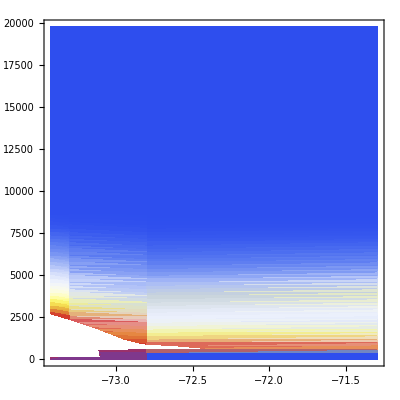

```mathematica
ListDensityPlot[test19, ColorFunction->"TemperatureMap"]
```

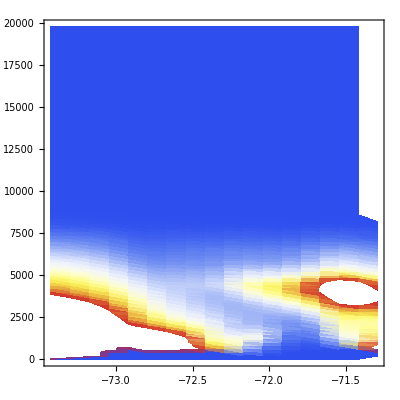

```mathematica
ListDensityPlot[work, ColorFunction->"TemperatureMap"]
```

```mathematica
ListDensityPlot[listphys⟦5⟧⟦4⟧,ClippingStyle->Automatic, PlotRange->Full,Frame->True,FrameLabel->{"Longitude (°)", "Height (m)"},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman")},GridLines->None, ColorFunction->"TemperatureMap", ImageSize->Large,PlotLabel -> microphysicslist⟦5⟧,PlotLegends->Placed[BarLegend[{"TemperatureMap",{0,Max[maxplot]}},LegendMargins->{{0,0},{10,5}},LegendLabel->"Snow mixing ratio (g kg^-1)",LabelStyle->FontFamily->"Times New Roman"],Right]];
```

```mathematica
ListDensityPlot[listphys⟦5⟧⟦4⟧,ClippingStyle->Automatic, PlotRange->Full,Frame->True,FrameLabel->{"Longitude (°)", "Height (m)"},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman")},GridLines->None, ColorFunction->ColorData[{"SunsetColors","Reverse"}], ImageSize->Large,PlotLabel -> microphysicslist⟦5⟧,PlotLegends->Placed[BarLegend[{ColorData[{"SunsetColors","Reverse"}],{0,Max[maxplot]}},LegendMargins->{{0,0},{10,5}},LegendLabel->"Snow mixing ratio (g kg^-1)",LabelStyle->FontFamily->"Times New Roman"],Right]];
```

```mathematica
crossM2M=ListDensityPlot[listphys⟦1⟧⟦6⟧, PlotRange->{{-73.42813,-71.29265},All,All},Frame->True,FrameLabel->{"Longitude (°)", "Height (m)"},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman")},GridLines->None, ColorFunction->"Rainbow",PlotRange -> {{All,All},{All,All}},ImageSize->250,PlotLabel -> microphysicslist⟦1⟧];
```

```mathematica
crossTHOM=ListDensityPlot[listphys⟦2⟧⟦6⟧, PlotRange->{{-73.42813,-71.29265},All,All},Frame->True,FrameLabel->{"Longitude (°)", "Height (m)"},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman")},GridLines->None, ColorFunction->"Rainbow",PlotRange -> {{All,All},{All,All}},ImageSize->250,PlotLabel -> microphysicslist⟦2⟧];
```

```mathematica
crossWDM6=ListDensityPlot[listphys⟦3⟧⟦6⟧, PlotRange->{{-73.42813,-71.29265},All,All},Frame->True,FrameLabel->{"Longitude (°)", "Height (m)"},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman")},GridLines->None, ColorFunction->"Rainbow",PlotRange -> {{All,All},{All,All}},ImageSize->250,PlotLabel -> microphysicslist⟦3⟧];
```

```mathematica
crossMILL=ListDensityPlot[listphys⟦4⟧⟦6⟧, PlotRange->{{-73.42813,-71.29265},All,All},Frame->True,FrameLabel->{"Longitude (°)", "Height (m)"},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman")},GridLines->None, ColorFunction->"Rainbow",PlotRange -> {{All,All},{All,All}},ImageSize->250,PlotLabel -> microphysicslist⟦4⟧];
```

```mathematica
crossGODD=ListDensityPlot[listphys⟦5⟧⟦6⟧, PlotRange->{{-73.42813,-71.29265},All,All},Frame->True,FrameLabel->{"Longitude (°)", "Height (m)"},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman")},GridLines->None, ColorFunction->"Rainbow",PlotRange -> {{All,All},{All,All}},ImageSize->250,PlotLabel -> microphysicslist⟦5⟧];
```

```mathematica
grid5=GraphicsGrid[{{crossM2M,crossTHOM,crossWDM6},{crossMILL,crossGODD}},Frame->True,PlotLabel->"Valid: 2019-01-20_05:00:00"];
```

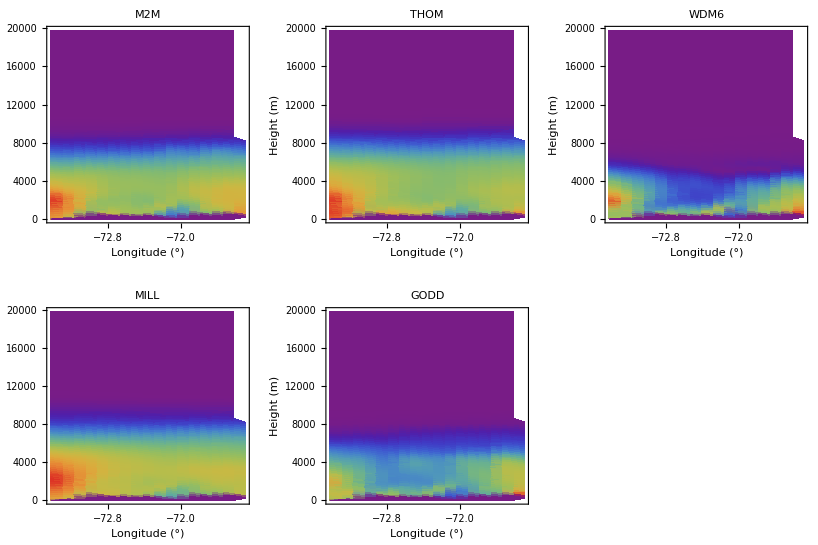

```mathematica
vertleg=BarLegend[{"Rainbow",{0,Max[maxplot]}},LegendMargins->{{0,0},{10,5}},LegendLabel->"Snow mixing ratio (g kg^-1)",LabelStyle->FontFamily->"Times New Roman"];
vertgrid5=Legended[grid5,Placed[vertleg,{Right,Right}]]
```

```mathematica
Export["vertgrid5.png",vertgrid5]
```

vertgrid5.png

```mathematica
crossM2M12=ListDensityPlot[listphys⟦1⟧⟦12⟧, PlotRange->{{-73.42813,-71.29265},All,All},Frame->True,FrameLabel->{"Longitude (°)", "Height (m)"},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman")},GridLines->None, ColorFunction->"Rainbow",PlotRange -> {{All,All},{All,All}},ImageSize->250,PlotLabel -> microphysicslist⟦1⟧];
```

```mathematica
crossTHOM12=ListDensityPlot[listphys⟦2⟧⟦12⟧, PlotRange->{{-73.42813,-71.29265},All,All},Frame->True,FrameLabel->{"Longitude (°)", "Height (m)"},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman")},GridLines->None, ColorFunction->"Rainbow",PlotRange -> {{All,All},{All,All}},ImageSize->250,PlotLabel -> microphysicslist⟦2⟧];
```

```mathematica
crossWDM612=ListDensityPlot[listphys⟦3⟧⟦12⟧, PlotRange->{{-73.42813,-71.29265},All,All},Frame->True,FrameLabel->{"Longitude (°)", "Height (m)"},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman")},GridLines->None, ColorFunction->"Rainbow",PlotRange -> {{All,All},{All,All}},ImageSize->250,PlotLabel -> microphysicslist⟦3⟧];
```

```mathematica
crossMILL12=ListDensityPlot[listphys⟦4⟧⟦12⟧, PlotRange->{{-73.42813,-71.29265},All,All},Frame->True,FrameLabel->{"Longitude (°)", "Height (m)"},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman")},GridLines->None, ColorFunction->"Rainbow",PlotRange -> {{All,All},{All,All}},ImageSize->250,PlotLabel -> microphysicslist⟦4⟧];
```

```mathematica
crossGODD12=ListDensityPlot[listphys⟦5⟧⟦12⟧, PlotRange->{{-73.42813,-71.29265},All,All},Frame->True,FrameLabel->{"Longitude (°)", "Height (m)"},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman")},GridLines->None, ColorFunction->"Rainbow",PlotRange -> {{All,All},{All,All}},ImageSize->250,PlotLabel -> microphysicslist⟦5⟧];
```

```mathematica
grid11=GraphicsGrid[{{crossM2M12,crossTHOM12,crossWDM612},{crossMILL12,crossGODD12}},Frame->True,PlotLabel->"Valid: 2019-01-20_11:00:00"];
```

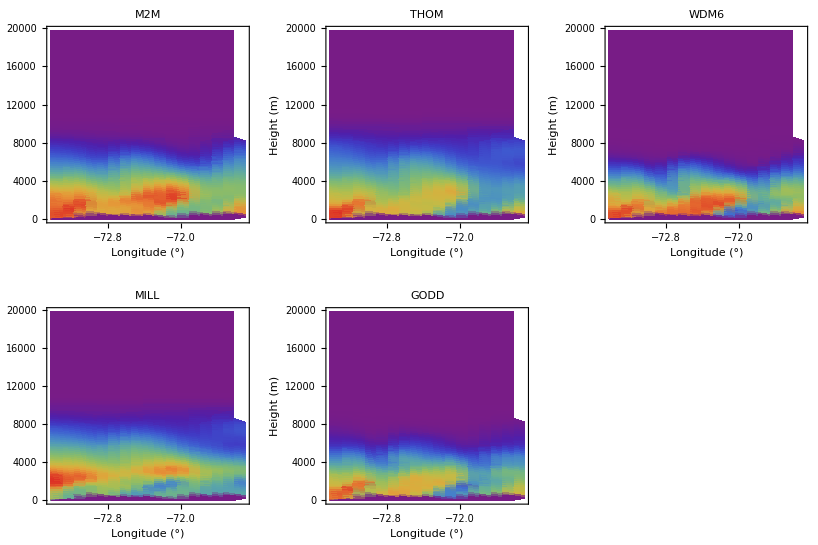

```mathematica
vertgrid11=Legended[grid11,Placed[vertleg,{Right,Right}]]
```

```mathematica
Export["vertgrid11.png",vertgrid11]
```

vertgrid11.png

## Total Accumulation Maps

```mathematica
M2M=Import["Images/M2M.png", ImageSize -> Large]
THOM=Import["Images/THOM.png", ImageSize -> Large];
WDM6=Import["Images/WDM6.png", ImageSize -> Large];
MILL=Import["Images/MILL.png", ImageSize -> Large];
GODD=Import["Images/GODD.png", ImageSize -> Large];
```

-Graphics-

```mathematica
accumgrid=Grid[{{M2M,THOM,WDM6},{MILL,GODD}},Frame->All]
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |

```mathematica
Export["accumgrid.png",accumgrid]
```

accumgrid.png

```mathematica
M2Mp=Import["M2M.pdf", ImageSize -> Medium];
THOMp=Import["THOM.pdf", ImageSize -> Medium];
WDM6p=Import["WDM6.pdf", ImageSize -> Medium];
MILLp=Import["MILL.pdf", ImageSize -> Medium];
GODDp=Import["GODD.pdf", ImageSize -> Medium];
```

```mathematica
MILLp
```

{-Graphics-}

```mathematica
M2Mp
```

{-Graphics-}

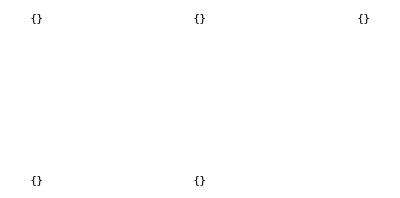

```mathematica
grid=GraphicsGrid[{{M2Mp,THOMp,WDM6p},{MILLp,GODDp}}]
```

```mathematica
accumgridp=Grid[{{M2Mp,THOMp,WDM6p},{MILLp,GODDp}},Frame->All]
```

{-Graphics-} | {-Graphics-} | {-Graphics-}
{-Graphics-} | {-Graphics-} |

```mathematica
mapsn={{-Graphics-, -Graphics-, -Graphics-}, {-Graphics-, -Graphics-, }}
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |

```mathematica
a={{-Graphics-, -Graphics-, -Graphics-}, {-Graphics-, -Graphics-, }}
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |

```mathematica
Export["accumgridp.jpeg",mapsn]
```

accumgridp.jpeg

```mathematica
(* entire domain plot*)
(*This plot plots the data that I have above*)
meansTHOMsnowmix=Table[Transpose[{means⟦time⟧,heights}],{time,1,24}];
Manipulate[ListPlot[meansTHOMsnowmix⟦time⟧,Frame->True,FrameLabel->{"Snow mixing ratio (g kg^-1)", "Height (m)"},PlotStyle->{Darker[Blue],Darker[Red],Darker[Green]},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman") }, Joined->True,GridLines->None
,PlotRange -> {{Automatic,All},{0,Automatic}},ImageSize->Large,PlotLegends->SwatchLegend[(*{"M2M",*)"THOM"(*,"WDM6"}*), LegendLabel ->"Microphysics scheme", LegendFunction->"Frame"] (*, Epilog->Inset[listTimes⟦2⟧,{Max[hydrometeor⟦type⟧⟦time⟧],19500}]*)],{time,2,24,1}];
```

```mathematica
a
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |

```mathematica
Export["map.png",a]
```

map.png

```mathematica
Export["map.jpg",a]
```

map.jpg

```mathematica
M2Mpg=Import["Images/M2Mg.pdf", ImageSize -> Medium];
THOMpg=Import["Images/THOMg.pdf", ImageSize -> Medium];
WDM6pg=Import["Images/WDM6g.pdf", ImageSize -> Medium];
MILLpg=Import["Images/MILLgr.pdf", ImageSize -> Medium];
GODDpg=Import["Images/GODDg.pdf", ImageSize -> Medium];
```

```mathematica
accumgridpg=Grid[{{M2Mpg,THOMpg,WDM6pg},{MILLpg,GODDpg}},Frame->All]
```

{-Graphics-} | {-Graphics-} | {-Graphics-}
{-Graphics-} | {-Graphics-} |

```mathematica
gr={{-Graphics-, -Graphics-, -Graphics-}, {-Graphics-, -Graphics-, }}
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |

```mathematica
ag={{-Graphics-, -Graphics-, -Graphics-}, {-Graphics-, -Graphics-, }}
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |

```mathematica
ag={{-Graphics-, -Graphics-, -Graphics-}, {-Graphics-, -Graphics-, }}
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |

```mathematica
Export["mapg.jpg",gr]
```

mapg.jpg

```mathematica
Plot[GammaDistribution[2,5],{x]
```

```mathematica
Plot[Table[PDF[GammaDistribution[α,2],x],{α,{1.5,4,6}}]//Evaluate,{x,0,20},PlotLabels->Automatic,ImageSize->Large]
```

-Graphics-

```mathematica
Plot[((6+α)(5+α)(4+α))/((3+α)(2+α)(1+α)),{α,-5,10},PlotRange->{-200,200}]
```

-Graphics-

```mathematica
n=1000000;
λ=1;
Plot[{n*d^2 ⅇ^(-λ*d)},{d,0,3*10^-1},PlotRange->Automatic]
```

-Graphics-

```mathematica
Plot[{n*d^8 ⅇ^(-λ*d)},{d,0,3*10^-1},PlotRange->All]
```

-Graphics-

```mathematica
Plot[Table[PDF[GammaDistribution[α,2],x],{α,{2,4,6}}]//Evaluate,{x,0,20}]
```

-Graphics-

```mathematica
partilcesizedensity=Plot[Table[PDF[GammaDistribution[α,.0000803],x],{α,{2,4,6}}]//Evaluate,{x,0,10^-3},Frame->True,FrameLabel->{"Diameter (m)", "Number Concentration Per Unit Volume"},PlotStyle->{Darker[Blue],Darker[Red],Darker[Green],Darker[Orange],Darker[Purple]},PlotStyle->Thickness[.003],LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman") },GridLines->None,PlotRange -> Automatic,ImageSize->Large,PlotLegends->SwatchLegend[{"2","4","6"}, LegendLabel ->"Shape Parameter α", LegendFunction->"Frame"] , Epilog->Style[Inset[listTimes⟦2⟧,{maxdbz-12,19500}],FontFamily->"Times New Roman",12],Filling->Axis]
```

-Graphics-

```mathematica
Export["psd.png",partilcesizedensity]
```

psd.png